```mathematica
SetDirectory["/home/muslem-rahimi/Doktorarbeit/Notes/LiteRed/Setup"];
<<LiteRed`
<<FeynCalc`
```

**************** LiteRed v1.82 ********************
Author: Roman N. Lee, Budker Institute of Nuclear Physics, Novosibirsk.
Release Date: 01.06.2015
LiteRed stands for Loop InTEgrals REDuction.
The package is designed for the search and application of the Integration-By-Part reduction rules. It also contains some other useful tools.
See ?LiteRed`* for a list of functions.

Factor1::shdw: Symbol Factor1 appears in multiple contexts {FeynCalc`,LiteRed`}; definitions in context FeynCalc` may shadow or be shadowed by other definitions.

Factor2::shdw: Symbol Factor2 appears in multiple contexts {FeynCalc`,LiteRed`}; definitions in context FeynCalc` may shadow or be shadowed by other definitions.

MetricTensor::shdw: Symbol MetricTensor appears in multiple contexts {FeynCalc`,Vectors`}; definitions in context FeynCalc` may shadow or be shadowed by other definitions.

FeynCalc 9.3.0 (stable version). For help, use the documentation center, check out the wiki or write to the mailing list.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, P3H-20-002, TTP19-020, TUM-EFT 130/19, arXiv:2001.04407

• V. Shtabovenko, R. Mertig and F. Orellana, Comput. Phys. Commun., 207, 432-444, 2016, arXiv:1601.01167

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun., 64, 345-359, 1991.

## Tensor reduction

### Master Integral

```mathematica
MasterIntegral[p_,α_,Δ_,β_]:=μ^(2*ϵ)*I*(-1)^(α+β)/(2^(d)*Pi^(d/2))*Gamma[α+d/2]*Gamma[β-α-d/2]/(Gamma[d/2]*Gamma[β])*Δ^(α-β+d/2)
```

### TwoLoop

```mathematica
FCClearScalarProducts[];
denrule={Den1[vk]^α1_*Den2[l]^α2_*Den3[k+l-v*ω]^α3_*Den4[k]^α4_*Den5[kl]^α5_-> j[MI,α1-1000,α2-1000,α3-1000,-α4+1000,-α5+1000]};
int1=-Tdec[{{el,μ},{el,ρ},{k,x}},{v},List->False]*GAD[x]*MTD[ν,σ]+Tdec[{{el,ν},{el,ρ},{k,x}},{v},List->False]*GAD[x]*MTD[μ,σ]+Tdec[{{el,μ},{el,σ},{k,x}},{v},List->False]*GAD[x]*MTD[ν,ρ]-Tdec[{{el,ν},{el,σ},{k,x}},{v},List->False]*GAD[x]*MTD[μ,ρ];

int2 = ω*Tdec[{{el,μ},{el,ρ},{v,x}},{v},List->False]*GAD[x]*MTD[ν,σ]-ω*Tdec[{{el,ν},{el,ρ},{v,x}},{v},List->False]*GAD[x]*MTD[μ,σ]-ω*Tdec[{{el,μ},{el,σ},{v,x}},{v},List->False]*GAD[x]*MTD[ν,ρ]+ ω*Tdec[{{el,ν},{el,σ},{v,x}},{v},List->False]*GAD[x]*MTD[μ,ρ];
int3=  -Tdec[{{el,μ},{el,ρ},{el,x}},{v},List->False]*GAD[x]*MTD[ν,σ]+Tdec[{{el,ν},{el,ρ},{el,x}},{v},List->False]*GAD[x]*MTD[μ,σ]+Tdec[{{el,μ},{el,σ},{el,x}},{v},List->False]*GAD[x]*MTD[ν,ρ]-Tdec[{{el,ν},{el,σ},{el,x}},{v},List->False]*GAD[x]*MTD[μ,ρ];

int = int1+int2+int3//Contract//Expand;


SPD[v,v]=1;
SPD[el,v]=vl;
SPD[el,el]=l2;
SPD[k,v]=kv;
SPD[k,el]=lk;

final=Den1[vk]*Den2[l]*Den3[l+k-v*ω]*int/.kv->Den1[vk]^(-1)/.l2->Den2[l]^(-1)/.lk->Den5[kl]/.vl->(-1/(2*ω))*(Den3[l+k-v*ω]^(-1)-Den4[k]-Den2[l]^(-1)-ω^2-2*Den5[kl]+2*Den1[vk]^(-1)*ω)//Expand;

final=Expand[Den1[vk]^1000*Den2[l]^1000*Den3[l+k-v*ω]^1000*Den4[k]^1000*Den5[kl]^1000*final]/.D->4/.d->4/.denrule;
```

##### Reduce to MIs

```mathematica
SetDim[d];
Declare[{p,q,k,v,l},Vector,{m,M,ω},Number]
NewBasis[MI,{sp[k,v],sp[l,l],sp[l+k-v*ω,l+k-v*ω],sp[k,k],sp[k,l]},{k,l},Directory->"shell2"]

sp[v,v]=1;
GenerateIBP[MI];
AnalyzeSectors[MI];
FindSymmetries[MI];
SolvejSector/@UniqueSectors[MI];
```

Valid basis.
    Ds[MI] — denominators,
    SPs[MI] — scalar products involving loop momenta,
    LMs[MI] — loop momenta,
    EMs[MI] — external momenta,
    Toj[MI] — rules to transform scalar products to denominators.
The definitions of the basis will be saved in shell2

DiskSave::overwrite: The file shell2/MI has been overwritten.

Integration-By-Part&Lorentz-Invariance identities are generated.
    IBP[MI] — integration-by-part identities,
    LI[MI] — Lorentz invariance identities.

Found 21 zero sectors out of 32.
    ZeroSectors[MI] — zero sectors,
    NonZeroSectors[MI] — nonzero sectors,
    SimpleSectors[MI] — simple sectors (no nonzero subsectors),
    BasisSectors[MI] — basis sectors (at least one immediate subsector is zero),
    ZerojRule[MI] — a rule to nullify all zero j[MI…],
    CutDs[MI] — a flag list of cut denominatorsj (1=cut).

Found 1 mapped sectors and 10 unique sectors.
    UniqueSectors[MI] — unique sectors.
    MappedSectors[MI] — mapped sectors.
    SR[MI][…] — symmetry relations for j[MI,…] from UniqueSectors[MI].
    jSymmetries[MI,…] — symmetry rules for the sector js[MI,…] in UniqueSectors[MI].
    jRules[MI,…] — reduction rules for j[MI,…] from MappedSectors[MI].

Sector js(MI,0,0,1,0,1)

DiskSave::overwrite: The file shell2/jRules[MI, 0, 0, 1, 0, 1] has been overwritten.

1 master integrals found:
j[MI, 0, 0, 1, 0, 1].
    jRules[MI, 0, 0, 1, 0, 1] — reduction rules for the sector.
    MIs[MI] — updated list of the masters.

Sector js(MI,0,0,1,1,1)

DiskSave::overwrite: The file shell2/jRules[MI, 0, 0, 1, 1, 1] has been overwritten.

0 master integrals found.
    jRules[MI, 0, 0, 1, 1, 1] — reduction rules for the sector.
    MIs[MI] — updated list of the masters.

Sector js(MI,0,1,1,1,0)

DiskSave::overwrite: The file shell2/jRules[MI, 0, 1, 1, 1, 0] has been overwritten.

General::stop: Further output of DiskSave::overwrite will be suppressed during this calculation.

1 master integrals found:
j[MI, 0, 1, 1, 1, 0].
    jRules[MI, 0, 1, 1, 1, 0] — reduction rules for the sector.
    MIs[MI] — updated list of the masters.

Sector js(MI,1,0,1,0,1)

0 master integrals found.
    jRules[MI, 1, 0, 1, 0, 1] — reduction rules for the sector.
    MIs[MI] — updated list of the masters.

Sector js(MI,1,1,1,0,0)

1 master integrals found:
j[MI, 1, 1, 1, 0, 0].
    jRules[MI, 1, 1, 1, 0, 0] — reduction rules for the sector.
    MIs[MI] — updated list of the masters.

Sector js(MI,0,1,1,1,1)

0 master integrals found.
    jRules[MI, 0, 1, 1, 1, 1] — reduction rules for the sector.
    MIs[MI] — updated list of the masters.

Sector js(MI,1,0,1,1,1)

0 master integrals found.
    jRules[MI, 1, 0, 1, 1, 1] — reduction rules for the sector.
    MIs[MI] — updated list of the masters.

Sector js(MI,1,1,1,0,1)

1 master integrals found:
j[MI, 1, 1, 1, 0, 1].
    jRules[MI, 1, 1, 1, 0, 1] — reduction rules for the sector.
    MIs[MI] — updated list of the masters.

Sector js(MI,1,1,1,1,0)

0 master integrals found.
    jRules[MI, 1, 1, 1, 1, 0] — reduction rules for the sector.
    MIs[MI] — updated list of the masters.

Sector js(MI,1,1,1,1,1)

0 master integrals found.
    jRules[MI, 1, 1, 1, 1, 1] — reduction rules for the sector.
    MIs[MI] — updated list of the masters.

```mathematica
(*test=IBPReduce[final]/.j[MI,1,1,1,0,0]->Master/.Master->(Exp[2*ϵ*EulerGamma]*Gamma[1-ϵ]^2*Gamma[1+4*ϵ])//Expand*)
gs=Sqrt[Subscript[α, S]*4*Pi];
Vorfaktor=CF*I^4*gs^2*Subscript[N, C];
Subscript[Δ, 1]=x*(1-x);
Master1= MasterIntegral[l,0,Subscript[Δ, 1],2]/.d->(4-2ϵ)//Simplify;
Subscript[Δ, 2]=λ^2-2*λ*ω;
Master2 = Master1*2*Gamma[1+ϵ]/Gamma[ϵ]*MasterIntegral[k,0,Subscript[Δ, 2],1+ϵ]//Simplify;
Master2=(-1)^(ϵ)*Integrate[Master2,{x,0,1},{λ,0,Infinity},GenerateConditions->False]/.d->(4-2ϵ)//Simplify

(*Master2=(-(μ^(4*ϵ)*2^(2 (4-2 ϵ)-4) (-ω)^(2 (4-2 ϵ)-5) Gamma[5-2 (4-2 ϵ)] Gamma[1/2 (4-2 ϵ)-1]^2)/Gamma[2 ϵ-1]);*)


test=IBPReduce[final]/.j[MI,1,1,1,0,0]->Master2//Expand;

test=Vorfaktor*Normal@Series[test/.d->(4-2ϵ),{ϵ,0,0}]//Expand;

(*test - Coefficient[test,ϵ]*ϵ //Expand*)

Coefficient[test,Log[-ω]]*Log[-ω]+Coefficient[test,Log[μ]]*Log[μ]/.Log[μ]->0/.Log[-ω]->Log[-ω/μ]//Simplify
```

(ω^3 (8 π)^(2 ϵ-3) μ^(4 ϵ) (-ω)^(-4 ϵ) csc(2 π ϵ) 1-ϵ 2 ϵ-3/2)/(3/2-ϵ)

-(ω^6 C_F N_C α_S log(-ω/μ) γ̄·v̄ ((ḡ)^μσ ((ḡ)^νρ-2 (v̄)^ν (v̄)^ρ)+2 (v̄)^μ ((v̄)^ρ (ḡ)^νσ-(v̄)^σ (ḡ)^νρ)-(ḡ)^μρ ((ḡ)^νσ-2 (v̄)^ν (v̄)^σ)))/(360 π^3)

```mathematica
(*Cross-Check*)
(*(ω^6 (Subscript[N, C]^2-1) Subscript[α, S] log(-ω/μ) (-(v̄)^ν (v̄)^σ (ḡ)^μρ+(v̄)^ν (v̄)^ρ (ḡ)^μσ+(v̄)^μ (v̄)^σ (ḡ)^νρ-(v̄)^μ (v̄)^ρ (ḡ)^νσ))/(360 π^3)-(ω^6 (Subscript[N, C]^2-1) Subscript[α, S] log(-ω/μ) ((ḡ)^μρ (ḡ)^νσ-(ḡ)^μσ (ḡ)^νρ))/(720 π^3)*)
```

### Quark-Quark-Condensate (dim3)

```mathematica
FCClearScalarProducts[];
denrule={Den1[vk]^α1_*Den2[k-v*ω]^α2_-> j[MI,α1-1000,α2-1000]};

Decomp[μ_,ρ_]:=Tdec[{{k,μ},{k,ρ}},{v},List->False]-Tdec[{{v,μ},{k,ρ}},{v},List->False]*ω-Tdec[{{k,μ},{v,ρ}},{v},List->False]*ω+Tdec[{{v,μ},{v,ρ}},{v},List->False]*ω^2

int = -Decomp[μ,ρ]*MTD[ν,σ]+Decomp[ν,ρ]*MTD[μ,σ]+Decomp[μ,σ]*MTD[ν,ρ]-Decomp[ν,σ]*MTD[μ,ρ];

(*int=-Tdec[{{el,μ},{el,ρ}},{v},List->False]*MTD[ν,σ]+Tdec[{{el,ν},{el,ρ}},{v},List->False]*MTD[μ,σ]+Tdec[{{el,μ},{el,σ}},{v},List->False]*MTD[ν,ρ]-Tdec[{{el,ν},{el,σ}},{v},List->False]*MTD[μ,ρ];
*)

final=int//Contract//Expand;

SPD[v,v]=1;
SPD[el,v]=vl;
SPD[el,el]=l2;
SPD[k,k]=k2;
SPD[k,v]=kv;
SPD[k,el]=lk;

final=Den1[vk]*Den2[k-v*ω]*int/.kv->Den1[vk]^(-1)/.k2->(Den2[k-v*ω]^(-1)-ω^2+2*Den1[vk]^(-1)*ω)//Expand;

final=Expand[Den1[vk]^1000*Den2[k-v*ω]^1000*final]/.denrule
```

(2 ω^2 j(MI,1,1) g^μσ g^νρ)/(1-D)-(2 ω^2 j(MI,1,1) g^μρ g^νσ)/(1-D)-(4 ω j(MI,0,1) g^μσ g^νρ)/(1-D)+(4 ω j(MI,0,1) g^μρ g^νσ)/(1-D)+(2 j(MI,-1,1) g^μσ g^νρ)/(1-D)-(2 j(MI,1,0) g^μσ g^νρ)/(1-D)-(2 j(MI,-1,1) g^μρ g^νσ)/(1-D)+(2 j(MI,1,0) g^μρ g^νσ)/(1-D)+(D ω^2 v^ν v^σ j(MI,1,1) g^μρ)/(1-D)-(D ω^2 v^ν v^ρ j(MI,1,1) g^μσ)/(1-D)-(D ω^2 v^μ v^σ j(MI,1,1) g^νρ)/(1-D)+(D ω^2 v^μ v^ρ j(MI,1,1) g^νσ)/(1-D)-(2 D ω v^ν v^σ j(MI,0,1) g^μρ)/(1-D)+(2 D ω v^ν v^ρ j(MI,0,1) g^μσ)/(1-D)+(2 D ω v^μ v^σ j(MI,0,1) g^νρ)/(1-D)-(2 D ω v^μ v^ρ j(MI,0,1) g^νσ)/(1-D)+(D v^ν v^σ j(MI,-1,1) g^μρ)/(1-D)-(v^ν v^σ j(MI,1,0) g^μρ)/(1-D)-(D v^ν v^ρ j(MI,-1,1) g^μσ)/(1-D)+(v^ν v^ρ j(MI,1,0) g^μσ)/(1-D)-(D v^μ v^σ j(MI,-1,1) g^νρ)/(1-D)+(v^μ v^σ j(MI,1,0) g^νρ)/(1-D)+(D v^μ v^ρ j(MI,-1,1) g^νσ)/(1-D)-(v^μ v^ρ j(MI,1,0) g^νσ)/(1-D)

##### Reduce to MIs

```mathematica
SetDim[d];
Declare[{p,q,k,v,l},Vector,{m,M,ω},Number]
NewBasis[MI,{sp[k,v],sp[k-v*ω,k-v*ω]},{k},Directory->"shell2"]

sp[v,v]=1;
GenerateIBP[MI];
AnalyzeSectors[MI];
FindSymmetries[MI];
SolvejSector/@UniqueSectors[MI];
```

NewBasis::ovrw: Warning: definitions for MI has been found. They may interfere with the upcoming definitions.

Valid basis.
    Ds[MI] — denominators,
    SPs[MI] — scalar products involving loop momenta,
    LMs[MI] — loop momenta,
    EMs[MI] — external momenta,
    Toj[MI] — rules to transform scalar products to denominators.
The definitions of the basis will be saved in shell2

DiskSave::overwrite: The file shell2/MI has been overwritten.

Integration-By-Part&Lorentz-Invariance identities are generated.
    IBP[MI] — integration-by-part identities,
    LI[MI] — Lorentz invariance identities.

Found 3 zero sectors out of 4.
    ZeroSectors[MI] — zero sectors,
    NonZeroSectors[MI] — nonzero sectors,
    SimpleSectors[MI] — simple sectors (no nonzero subsectors),
    BasisSectors[MI] — basis sectors (at least one immediate subsector is zero),
    ZerojRule[MI] — a rule to nullify all zero j[MI…],
    CutDs[MI] — a flag list of cut denominatorsj (1=cut).

Found 0 mapped sectors and 1 unique sectors.
    UniqueSectors[MI] — unique sectors.
    MappedSectors[MI] — mapped sectors.
    SR[MI][…] — symmetry relations for j[MI,…] from UniqueSectors[MI].
    jSymmetries[MI,…] — symmetry rules for the sector js[MI,…] in UniqueSectors[MI].
    jRules[MI,…] — reduction rules for j[MI,…] from MappedSectors[MI].

Sector js(MI,1,1)

DiskSave::overwrite: The file shell2/jRules[MI, 1, 1] has been overwritten.

1 master integrals found:
j[MI, 1, 1].
    jRules[MI, 1, 1] — reduction rules for the sector.
    MIs[MI] — updated list of the masters.

```mathematica
Subscript[g, S]=Subscript[α, S]*4*Pi;
Vorfaktor=CF*I^3*Subscript[g, S]*
1/4;

test=IBPReduce[final]//Expand;
Master1=2*Vorfaktor*Integrate[MasterIntegral[k,0,λ^2-2*λ*ω,2],{λ,0,Infinity},GenerateConditions->False]/.d->(4-2ϵ);

test=test/.j[MI,1,1]->Master1/.D->(4-2ϵ);
test = Normal@Series[test,{ϵ,0,0}];
test=Coefficient[test,Log[-ω]]*Log[-ω]+Coefficient[test,Log[μ]]*Log[μ]/.Log[μ]->0/.Log[-ω]->Log[-ω/μ]//Simplify
```

(ω^3 C_F α_S log(-ω/μ) (g^μσ g^νρ-g^μρ g^νσ+2 v^ν (v^σ g^μρ-v^ρ g^μσ)+v^μ (2 v^ρ g^νσ-2 v^σ g^νρ)))/(6 π)

```mathematica
(ω^3 Subscript[C, F] Subscript[α, S] log(-ω/μ) ((ḡ)^μσ (ḡ)^νρ-(ḡ)^μρ (ḡ)^νσ+2 (v̄)^ν ((v̄)^σ (ḡ)^μρ-(v̄)^ρ (ḡ)^μσ)+(v̄)^μ (2 (v̄)^ρ (ḡ)^νσ-2 (v̄)^σ (ḡ)^νρ)))/(6 π)
```

-(ω^4 log α_S ((ḡ)^(μ σ+ν ρ)-(ḡ)^(μ ρ+ν σ)+(v̄)^μ (2 (v̄)^ρ (ḡ)^(ν σ)-2 (v̄)^σ (ḡ)^(ν ρ))+2 (v̄)^ν ((v̄)^σ (ḡ)^(μ ρ)-(v̄)^ρ (ḡ)^(μ σ))) C_{-1/4 x1 (x1 x3+4 x2 ω (x3-x2))})/(6 π μ)

### Gluon-Gluon-Condensate (dim4)

```mathematica
FCClearScalarProducts[];
denrule={Den1[vk]^α1_*Den2[k-v*ω]^α2_-> j[MI,α1-1000,α2-1000]};
int=(Tdec[{{k,x}},{v},List->False]-ω*Tdec[{{v,x}},{v},List->False])*GAD[x]*(MTD[μ,ρ]*MTD[ν,σ]-MTD[μ,σ]*MTD[ρ,ν])//Contract//Expand;



SPD[v,v]=1;
SPD[el,v]=vl;
SPD[el,el]=l2;
SPD[k,v]=kv;
SPD[k,el]=lk;

final=Den1[vk]*Den2[k-v*ω]*int/.kv->Den1[vk]^(-1)//Expand;

final=Expand[Den1[vk]^1000*Den2[k-v*ω]^1000*final]/.denrule
```

ω j(MI,1,1) g^μσ g^νρ γ·v-ω j(MI,1,1) g^μρ g^νσ γ·v+j(MI,0,1) g^μσ g^νρ (-(γ·v))+j(MI,0,1) g^μρ g^νσ γ·v

##### Reduce to MIs

```mathematica
SetDim[d];
Declare[{p,q,k,v,l},Vector,{m,M,ω},Number]
NewBasis[MI,{sp[k,v],sp[k-v*ω,k-v*ω]},{k},Directory->"shell2"]

sp[v,v]=1;
GenerateIBP[MI];
AnalyzeSectors[MI];
FindSymmetries[MI];
SolvejSector/@UniqueSectors[MI];
```

NewBasis::ovrw: Warning: definitions for MI has been found. They may interfere with the upcoming definitions.

Valid basis.
    Ds[MI] — denominators,
    SPs[MI] — scalar products involving loop momenta,
    LMs[MI] — loop momenta,
    EMs[MI] — external momenta,
    Toj[MI] — rules to transform scalar products to denominators.
The definitions of the basis will be saved in shell2

DiskSave::overwrite: The file shell2/MI has been overwritten.

Integration-By-Part&Lorentz-Invariance identities are generated.
    IBP[MI] — integration-by-part identities,
    LI[MI] — Lorentz invariance identities.

Found 3 zero sectors out of 4.
    ZeroSectors[MI] — zero sectors,
    NonZeroSectors[MI] — nonzero sectors,
    SimpleSectors[MI] — simple sectors (no nonzero subsectors),
    BasisSectors[MI] — basis sectors (at least one immediate subsector is zero),
    ZerojRule[MI] — a rule to nullify all zero j[MI…],
    CutDs[MI] — a flag list of cut denominatorsj (1=cut).

Found 0 mapped sectors and 1 unique sectors.
    UniqueSectors[MI] — unique sectors.
    MappedSectors[MI] — mapped sectors.
    SR[MI][…] — symmetry relations for j[MI,…] from UniqueSectors[MI].
    jSymmetries[MI,…] — symmetry rules for the sector js[MI,…] in UniqueSectors[MI].
    jRules[MI,…] — reduction rules for j[MI,…] from MappedSectors[MI].

Sector js(MI,1,1)

DiskSave::overwrite: The file shell2/jRules[MI, 1, 1] has been overwritten.

1 master integrals found:
j[MI, 1, 1].
    jRules[MI, 1, 1] — reduction rules for the sector.
    MIs[MI] — updated list of the masters.

```mathematica
ClearAll[d];
gs=Sqrt[Subscript[α, S]*4*Pi];
Subscript[C, F]=(Subscript[N, C]^2-1)/(2*Subscript[N, C]);
Vorfaktor=I^3*gs^2*Subscript[N, C]*Subscript[C, F]*1/(d*(d-1)*(Subscript[N, C]^2-1));
Subscript[Δ, 1]=λ^2-2*λ*ω;
Master =2*Vorfaktor* MasterIntegral[k,0,Subscript[Δ, 1],2]/.d->(4-2*ϵ);
GG=IBPReduce[final]//Expand

GG=GG/.j[MI,1,1]->Master

GG = Integrate[GG,{λ,0,Infinity},Assumptions->{0<a<0.01},GenerateConditions->False];

GG=Normal@Series[GG,{ϵ,0,0}]

GG=Coefficient[GG,Log[-ω]]*Log[-ω]+Coefficient[GG,Log[μ]]*Log[μ]/.Log[μ]->0/.Log[-ω]->Log[-ω/μ]//Simplify
```

ω j(MI,1,1) g^μσ g^νρ γ·v-ω j(MI,1,1) g^μρ g^νσ γ·v

(ω 2^(2 ϵ-2) π^(1/2 (2 ϵ-4)+1) α_S μ^(2 ϵ) 1/2 (2 ϵ-4)+2 g^μσ g^νρ γ·v (λ^2-2 λ ω)^(1/2 (4-2 ϵ)-2))/((3-2 ϵ) (4-2 ϵ))-(ω 2^(2 ϵ-2) π^(1/2 (2 ϵ-4)+1) α_S μ^(2 ϵ) 1/2 (2 ϵ-4)+2 g^μρ g^νσ γ·v (λ^2-2 λ ω)^(1/2 (4-2 ϵ)-2))/((3-2 ϵ) (4-2 ϵ))

Integrate::fas: Warning: one or more assumptions evaluated to False.

Integrate::idiv: Integral of -(ω γ·v (-6-7 ϵ+6 ℽ ϵ-12 ϵ log(2)-6 ϵ log(π)-12 ϵ log(μ)+6 ϵ log(λ (λ-2 ω))) (g^μσ g^νρ-g^μρ g^νσ) α_S)/(288 π ϵ) does not converge on {0,∞}.

Integrate[(ω 2^(2 ϵ-2) π^(1/2 (2 ϵ-4)+1) α_S μ^(2 ϵ) 1/2 (2 ϵ-4)+2 g^μσ g^νρ γ·v (λ^2-2 λ ω)^(1/2 (4-2 ϵ)-2))/((3-2 ϵ) (4-2 ϵ))-(ω 2^(2 ϵ-2) π^(1/2 (2 ϵ-4)+1) α_S μ^(2 ϵ) 1/2 (2 ϵ-4)+2 g^μρ g^νσ γ·v (λ^2-2 λ ω)^(1/2 (4-2 ϵ)-2))/((3-2 ϵ) (4-2 ϵ)),{λ,0,∞},Assumptions→{False},GenerateConditions→False]

0

### Quark-Gluon-Condensate (dim5)

```mathematica
(DiracSlash[k]-DiracSlash[v]*ω).((FV[k,σ]-ω*FV[v,σ]).MT[ρ,λ]-(FV[k,ρ]-ω*FV[v,ρ]).MT[σ,λ]).GA[λ]//Contract//ExpandScalarProduct//Expand
```

(k̄)^ρ (-(γ̄·k̄-ω γ̄·v̄).(γ̄)^σ)+ω (v̄)^ρ (γ̄·k̄-ω γ̄·v̄).(γ̄)^σ+(k̄)^σ (γ̄·k̄-ω γ̄·v̄).(γ̄)^ρ-ω (v̄)^σ (γ̄·k̄-ω γ̄·v̄).(γ̄)^ρ

##### Gluon x to z -Graphics-

```mathematica
FCClearScalarProducts[];
denrule={Den1[vk]^α1_*Den2[k-v*ω]^α2_-> j[MI,α1-1000,α2-1000]};

int1=-GAD[σ].Tdec[{{k,ρ},{k,x}},{v},List->False].GAD[x]+GAD[ρ].Tdec[{{k,σ},{k,x}},{v},List->False].GAD[x];

int2 =ω*GAD[σ].Tdec[{{k,ρ},{v,x}},{v},List->False].GAD[x]+ω*GAD[σ].Tdec[{{v,ρ},{k,x}},{v},List->False].GAD[x]-ω*GAD[ρ].Tdec[{{k,σ},{v,x}},{v},List->False].GAD[x]-ω*GAD[ρ].Tdec[{{v,σ},{k,x}},{v},List->False].GAD[x];

int3 = -ω^2*GAD[σ].Tdec[{{v,ρ},{v,x}},{v},List->False].GAD[x]+ ω^2*GAD[ρ].Tdec[{{v,σ},{v,x}},{v},List->False].GAD[x];

final1= int1+int2+int3//Contract//Expand;
SPD[v,v]=1;
SPD[el,v]=vl;
SPD[el,el]=l2;
SPD[k,k]=k2;
SPD[k,v]=kv;
SPD[k,el]=lk;

final1=Den1[vk]*Den2[k-v*ω]^2*final1/.kv->Den1[vk]^(-1)/.k2->(Den2[k-v*ω]^(-1)-ω^2+2*Den1[vk]^(-1))//Expand;

final1=Expand[Den1[vk]^1000*Den2[k-v*ω]^1000*final1]/.denrule/.D->4
```

-1/3 ω^2 j(MI,1,2) (γ̄)^ρ.(γ̄)^σ+1/3 ω^2 j(MI,1,2) (γ̄)^σ.(γ̄)^ρ-1/3 j(MI,-1,2) (γ̄)^ρ.(γ̄)^σ+1/3 j(MI,-1,2) (γ̄)^σ.(γ̄)^ρ+2/3 j(MI,0,2) (γ̄)^ρ.(γ̄)^σ-2/3 j(MI,0,2) (γ̄)^σ.(γ̄)^ρ+1/3 j(MI,1,1) (γ̄)^ρ.(γ̄)^σ-1/3 j(MI,1,1) (γ̄)^σ.(γ̄)^ρ-4/3 ω^2 (v̄)^ρ j(MI,1,2) (γ̄)^σ.(γ̄·v̄)+4/3 ω^2 (v̄)^σ j(MI,1,2) (γ̄)^ρ.(γ̄·v̄)+2 ω (v̄)^ρ j(MI,0,2) (γ̄)^σ.(γ̄·v̄)-2 ω (v̄)^σ j(MI,0,2) (γ̄)^ρ.(γ̄·v̄)-4/3 (v̄)^ρ j(MI,-1,2) (γ̄)^σ.(γ̄·v̄)+2/3 (v̄)^ρ j(MI,0,2) (γ̄)^σ.(γ̄·v̄)+1/3 (v̄)^ρ j(MI,1,1) (γ̄)^σ.(γ̄·v̄)+4/3 (v̄)^σ j(MI,-1,2) (γ̄)^ρ.(γ̄·v̄)-2/3 (v̄)^σ j(MI,0,2) (γ̄)^ρ.(γ̄·v̄)-1/3 (v̄)^σ j(MI,1,1) (γ̄)^ρ.(γ̄·v̄)

##### Gluon 0 to z -Graphics-

```mathematica
FCClearScalarProducts[];
denrule={Den1[vk]^α1_*Den2[k-v*ω]^α2_-> j[MI,α1-1000,α2-1000]};

int1=Tdec[{{k,μ},{k,x}},{v},List->False].GAD[x].GAD[ν]-Tdec[{{k,ν},{k,x}},{v},List->False].GAD[x].GAD[μ];

int2 =-ω*Tdec[{{k,μ},{v,x}},{v},List->False].GAD[x].GAD[ν]-ω*Tdec[{{v,μ},{k,x}},{v},List->False].GAD[x].GAD[ν]+ω*Tdec[{{k,ν},{v,x}},{v},List->False].GAD[x].GAD[μ]+ω*Tdec[{{v,ν},{k,x}},{v},List->False].GAD[x].GAD[μ];

int3 = ω^2*Tdec[{{v,μ},{v,x}},{v},List->False].GAD[x].GAD[ν] - ω^2*Tdec[{{v,ν},{v,x}},{v},List->False].GAD[x].GAD[μ];

final2= int1+int2+int3//Contract//Expand;
SPD[v,v]=1;
SPD[el,v]=vl;
SPD[el,el]=l2;
SPD[k,k]=k2;
SPD[k,v]=kv;
SPD[k,el]=lk;

final2=Den1[vk]*Den2[k-v*ω]^2*final2/.kv->Den1[vk]^(-1)/.k2->(Den2[k-v*ω]^(-1)-ω^2+2*Den1[vk]^(-1))//Expand;

final2=Expand[Den1[vk]^1000*Den2[k-v*ω]^1000*final2]/.denrule/.D->4;
```

##### Triple gluon vertex -Graphics-

```mathematica
FCClearScalarProducts[];
denrule={Den1[vk]^α1_*Den2[k-v*ω]^α2_-> j[MI,α1-1000,α2-1000]};
sigma[μ_,ν_] := I/2*(GA[μ].GA[ν] - GA[ν].GA[μ])
Denom1 = (((FV[-k,ρ] + ω*FV[v,ρ])*MT[σ,α] - (FV[-k,σ] + ω*FV[v,σ])*MT[ρ,α])*((MT[β,γ]*MT[α,χ] - MT[γ,α]*MT[β,χ])*(-MT[ν,γ]*(FV[-k,μ] + ω*FV[v,μ]) + MT[μ,γ]*(FV[-k,ν] + ω*FV[v,ν])) + (MT[α,β]*(FV[-k,γ] + ω*FV[v,γ]) + MT[β,γ]*(FV[-k,α] + ω*FV[v,α]) - 2*MT[γ,α]*(FV[-k,β] + ω*FV[v,β]))*(-MT[ν,γ]*MT[μ,χ] + MT[μ,γ]*MT[ν,χ]))).sigma[χ,β] //Contract //Expand;
Tdec[{{k,μ},{k,x}},{v},List->False].GAD[x].GAD[ν];

Decomp1[β_,ρ_,μ_,χ_,ν_,σ_] := Tdec[{{k,β},{k,ρ}},{v},List->False].MTD[μ,χ].MTD[ν,σ]

Decomp2[β_,ρ_,μ_,χ_,ν_,σ_] := Tdec[{{v,β},{k,ρ}},{v},List->False].MTD[μ,χ].MTD[ν,σ]

Decomp3[β_,ρ_,μ_,χ_,ν_,σ_] := Tdec[{{v,β},{v,ρ}},{v},List->False].MTD[μ,χ].MTD[ν,σ]

sigma[μ_,ν_] := I/2*(GAD[μ].GAD[ν] - GAD[ν].GAD[μ]);

int1 = (2*Decomp1[β,ρ,μ,χ,ν,σ] + Decomp1[μ,ρ,β,χ,ν,σ] - 2*Decomp1[β,ρ,μ,σ,ν,χ] + Decomp1[μ,ρ,β,σ,ν,χ] - Decomp1[ν,ρ,μ,σ,β,χ] - Decomp1[ν,ρ,μ,χ,β,σ] - Decomp1[μ,ρ,β,ν,χ,σ] + Decomp1[ν,ρ,σ,χ,β,μ] -2*Decomp1[β,σ,μ,χ,ν,ρ] - Decomp1[μ,σ,β,χ,ν,ρ] + 2*Decomp1[β,σ,ν,χ,μ,ρ] - Decomp1[μ,σ,β,ρ,ν,χ] + Decomp1[ν,σ,β,χ,μ,ρ] + Decomp1[ν,σ,β,ρ,μ,χ] + Decomp1[μ,σ,β,ν,ρ,χ] - Decomp1[ν,σ,μ,β,ρ,χ]) //Contract //Simplify ;

int2 = ω*(-2*Decomp2[β,ρ,μ,χ,ν,σ] - Decomp2[μ,ρ,β,χ,ν,σ] + 2*Decomp2[β,ρ,μ,σ,ν,χ] - Decomp2[μ,ρ,β,σ,ν,χ] + Decomp2[ν,ρ,μ,σ,β,χ] + Decomp2[ν,ρ,μ,χ,β,σ] + Decomp2[μ,ρ,σ,χ,ν,β] - Decomp2[ν,ρ,μ,β,χ,σ] - 2*Decomp2[ρ,β,μ,χ,ν,σ] - Decomp2[ρ,μ,β,χ,ν,σ] + 2*Decomp2[ρ,β,μ,σ,ν,χ] - Decomp2[ρ,μ,ν,χ,β,σ] + Decomp2[ρ,ν,β,χ,μ,σ] + Decomp2[ρ,ν,μ,χ,β,σ] + Decomp2[ρ,μ,σ,χ,ν,β] - Decomp2[ρ,ν,σ,χ,β,μ] + 2*Decomp2[β,σ,μ,χ,ν,ρ] + Decomp2[μ,σ,β,χ,ν,ρ] -2*Decomp2[β,σ,μ,ρ,ν,χ] + Decomp2[μ,σ,ν,χ,β,ρ] - Decomp2[ν,σ,μ,ρ,β,χ] - Decomp2[ν,σ,μ,χ,β,ρ] - Decomp2[μ,σ,ρ,χ,ν,β] + Decomp2[ν,σ,μ,β,ρ,χ] + 2*Decomp2[σ,β,μ,χ,ν,ρ] + Decomp2[σ,μ,β,χ,ν,ρ] - 2*Decomp2[σ,β,μ,ρ,ν,χ] + Decomp2[σ,μ,ν,χ,β,ρ] - Decomp2[σ,ν,μ,ρ,β,χ] - Decomp2[σ,ν,μ,χ,β,ρ] - Decomp2[σ,μ,ρ,χ,ν,β] + Decomp2[σ,ν,ρ,χ,β,μ])//Contract //Simplify ;

int3 = ω^2*(2*Decomp3[β,ρ,μ,χ,ν,σ] + Decomp3[μ,ρ,β,χ,ν,σ] - 2*Decomp3[β,ρ,μ,σ,ν,χ] + Decomp3[μ,ρ,β,σ,ν,χ] - Decomp3[ν,ρ,μ,σ,β,χ] - Decomp3[ν,ρ,μ,χ,β,σ] - Decomp3[μ,ρ,β,ν,χ,σ] + Decomp3[ν,ρ,σ,χ,β,μ] -2*Decomp3[β,σ,μ,χ,ν,ρ] - Decomp3[μ,σ,β,χ,ν,ρ] + 2*Decomp3[β,σ,ν,χ,μ,ρ] - Decomp3[μ,σ,β,ρ,ν,χ] + Decomp3[ν,σ,β,χ,μ,ρ] + Decomp3[ν,σ,β,ρ,μ,χ] + Decomp3[μ,σ,β,ν,ρ,χ] - Decomp3[ν,σ,μ,β,ρ,χ]) //Contract //Simplify ;

final3= (int1 + int2 + int3).sigma[χ,β] //Contract//Expand;
SPD[v,v]=1;
SPD[el,v]=vl;
SPD[el,el]=l2;
SPD[k,k]=k2;
SPD[k,v]=kv;
SPD[k,el]=lk;

final3=Den1[vk]*Den2[k-v*ω]^2*final3/.kv->Den1[vk]^(-1)/.k2->(Den2[k-v*ω]^(-1)-ω^2+2*Den1[vk]^(-1))//Expand;

final3=Expand[Den1[vk]^1000*Den2[k-v*ω]^1000*final3]/.denrule/.D->4;
```

##### Reduce to MIs

```mathematica
SetDim[d];
Declare[{p,q,k,v,l},Vector,{m,M,ω},Number]
NewBasis[MI,{sp[k,v],sp[k-v*ω,k-v*ω]},{k},Directory->"shell2"]

sp[v,v]=1;
GenerateIBP[MI];
AnalyzeSectors[MI];
FindSymmetries[MI];
SolvejSector/@UniqueSectors[MI];
```

Valid basis.
    Ds[MI] — denominators,
    SPs[MI] — scalar products involving loop momenta,
    LMs[MI] — loop momenta,
    EMs[MI] — external momenta,
    Toj[MI] — rules to transform scalar products to denominators.
The definitions of the basis will be saved in shell2

DiskSave::overwrite: The file shell2/MI has been overwritten.

Integration-By-Part&Lorentz-Invariance identities are generated.
    IBP[MI] — integration-by-part identities,
    LI[MI] — Lorentz invariance identities.

Found 3 zero sectors out of 4.
    ZeroSectors[MI] — zero sectors,
    NonZeroSectors[MI] — nonzero sectors,
    SimpleSectors[MI] — simple sectors (no nonzero subsectors),
    BasisSectors[MI] — basis sectors (at least one immediate subsector is zero),
    ZerojRule[MI] — a rule to nullify all zero j[MI…],
    CutDs[MI] — a flag list of cut denominatorsj (1=cut).

Found 0 mapped sectors and 1 unique sectors.
    UniqueSectors[MI] — unique sectors.
    MappedSectors[MI] — mapped sectors.
    SR[MI][…] — symmetry relations for j[MI,…] from UniqueSectors[MI].
    jSymmetries[MI,…] — symmetry rules for the sector js[MI,…] in UniqueSectors[MI].
    jRules[MI,…] — reduction rules for j[MI,…] from MappedSectors[MI].

Sector js(MI,1,1)

DiskSave::overwrite: The file shell2/jRules[MI, 1, 1] has been overwritten.

1 master integrals found:
j[MI, 1, 1].
    jRules[MI, 1, 1] — reduction rules for the sector.
    MIs[MI] — updated list of the masters.

```mathematica
gs=Sqrt[Subscript[α, S]*4*Pi];
Vorfaktor=CF*I^4*gs^2*
1/(48);

qGCondensate1=IBPReduce[final1]//Expand;
Master1=2*Vorfaktor*Integrate[MasterIntegral[k,0,λ^2-2*λ*ω,2],{λ,0,Infinity},GenerateConditions->False]/.d->(4-2ϵ);

qGCondensate1=qGCondensate1/.j[MI,1,1]->Master1/.d->(4-2ϵ);
qGCondensate1= Normal@Series[qGCondensate1,{ϵ,0,0}];
qGCondensate1=Coefficient[qGCondensate1,Log[-ω]]*Log[-ω]+Coefficient[qGCondensate1,Log[μ]]*Log[μ]/.Log[μ]->0/.Log[-ω]->Log[-ω/μ]//Simplify
```

-(ⅈ ω C_F α_S log(-ω/μ) ((γ̄)^ρ.(γ̄)^σ-(γ̄)^σ.(γ̄)^ρ+2 (v̄)^ρ (γ̄)^σ.(γ̄·v̄)-2 (v̄)^σ (γ̄)^ρ.(γ̄·v̄)))/(96 π)

```mathematica
(*Cross-Check*)
(*(ⅈ qGC ω Subscript[C, F] Subscript[α, S] log(-ω/μ) ((γ̄)^ρ.(γ̄)^σ-(γ̄)^σ.(γ̄)^ρ-2 (v̄)^ρ (γ̄)^σ.(γ̄·v̄)+2 (v̄)^σ (γ̄)^ρ.(γ̄·v̄)))/(96 π)*)
```

```mathematica
qGCondensate2=IBPReduce[final2]//Expand;
Master1=2*Vorfaktor*Integrate[MasterIntegral[k,0,λ^2-2*λ*ω,2],{λ,0,Infinity},GenerateConditions->False]/.d->(4-2ϵ);

qGCondensate2=qGCondensate2/.j[MI,1,1]->Master1/.d->(4-2ϵ);
qGCondensate2= Normal@Series[qGCondensate2,{ϵ,0,0}];
qGCondensate2=Coefficient[qGCondensate2,Log[-ω]]*Log[-ω]+Coefficient[qGCondensate2,Log[μ]]*Log[μ]/.Log[μ]->0/.Log[-ω]->Log[-ω/μ]//Simplify
```

-(ⅈ ω C_F α_S log(-ω/μ) ((γ̄)^μ.(γ̄)^ν-(γ̄)^ν.(γ̄)^μ-2 (v̄)^μ (γ̄·v̄).(γ̄)^ν+2 (v̄)^ν (γ̄·v̄).(γ̄)^μ))/(96 π)

```mathematica
gs=Sqrt[Subscript[α, S]*4*Pi];
Vorfaktor=-I/2*I*CF*CA^2*gs^2/2*
1/(48)*1/4;

qGCondensate3=IBPReduce[final3]//Expand;
Master1=2*Vorfaktor*Integrate[MasterIntegral[k,0,λ^2-2*λ*ω,2],{λ,0,Infinity},GenerateConditions->False]/.d->(4-2ϵ);

qGCondensate3=qGCondensate3/.j[MI,1,1]->Master1/.d->(4-2ϵ);
qGCondensate3= Normal@Series[qGCondensate3,{ϵ,0,0}];
qGCondensate3=Coefficient[qGCondensate3,Log[-ω]]*Log[-ω]+Coefficient[qGCondensate3,Log[μ]]*Log[μ]/.Log[μ]->0/.Log[-ω]->Log[-ω/μ]//Simplify
```

1/(768 π)ω C_A^2 C_F α_S log(-ω/μ) (-(γ̄)^ν.(γ̄)^ρ (ḡ)^μσ+(γ̄)^ρ.(γ̄)^ν (ḡ)^μσ-(γ̄)^μ.(γ̄)^σ (ḡ)^νρ+(γ̄)^σ.(γ̄)^μ (ḡ)^νρ+(γ̄)^μ.(γ̄)^ρ (ḡ)^νσ-(γ̄)^ρ.(γ̄)^μ (ḡ)^νσ+(γ̄)^ν.(γ̄)^σ ((ḡ)^μρ-(v̄)^μ (v̄)^ρ)+(γ̄)^σ.(γ̄)^ν ((v̄)^μ (v̄)^ρ-(ḡ)^μρ)+(v̄)^ρ (ḡ)^μσ (γ̄)^ν.(γ̄·v̄)-(v̄)^ρ (ḡ)^μσ (γ̄·v̄).(γ̄)^ν-(v̄)^ρ (ḡ)^νσ (γ̄)^μ.(γ̄·v̄)+(v̄)^ρ (ḡ)^νσ (γ̄·v̄).(γ̄)^μ-(v̄)^σ (ḡ)^μρ (γ̄)^ν.(γ̄·v̄)+(v̄)^σ (ḡ)^μρ (γ̄·v̄).(γ̄)^ν+(v̄)^σ (ḡ)^νρ (γ̄)^μ.(γ̄·v̄)-(v̄)^σ (ḡ)^νρ (γ̄·v̄).(γ̄)^μ+(v̄)^ν (v̄)^ρ (γ̄)^μ.(γ̄)^σ-(v̄)^ν (v̄)^ρ (γ̄)^σ.(γ̄)^μ+(v̄)^μ (v̄)^σ (γ̄)^ν.(γ̄)^ρ-(v̄)^μ (v̄)^σ (γ̄)^ρ.(γ̄)^ν-(v̄)^ν (v̄)^σ (γ̄)^μ.(γ̄)^ρ+(v̄)^ν (v̄)^σ (γ̄)^ρ.(γ̄)^μ)

## Nishikawa,Tanaka sum rule

### qqbar condensate

```mathematica
A=1/2*(w*λ+λ^2/8);
d=4-2*eps;

test1=Integrate[A^(-2+d/2),{λ,0,Infinity},GenerateConditions->False]
```

(2 w^(1-2 eps) 1-eps eps-1/2)/(√π)

```mathematica
Subscript[C3H, q]=Series[1/4*Subscript[α, S]*4*Pi*Subscript[C, F]*μ^(2*eps)*test1/d*1/(2^d*Pi^(d/2))*Gamma[1+d/2]*Gamma[2-d/2]/(Gamma[d/2]*Gamma[3]),{eps,0,0}]//FullSimplify
```

-(w C_F α_S)/(16 π eps)+(w C_F α_S (-2 log(μ)+2 log(w)+ℽ-2-log(π)))/(16 π)+O(eps^1)

```mathematica
test2=Integrate[A^(-3+d/2)*λ^2,{λ,0,Infinity},GenerateConditions->False]

Series[-μ^(2*eps)*test2*1/16*1/(2^d*Pi^(d/2))*Gamma[3-d/2]/(Gamma[3]),{eps,0,0}]//FullSimplify
```

(2^(7-2 eps) w^(1-2 eps) 2-eps 2 eps-1)/(eps+1)

w/(8 π^2 eps)+(w (2 log(μ)-2 log(w)-ℽ+1+log(π)))/(8 π^2)+O(eps^1)

```mathematica
(1+DiracSlash[v])/2*DiracSlash[v]//DiracSimplify
```

1/2 (γ̄·v̄)^2+(γ̄·v̄)/2

## Diagonal hadronic matrix element

### Two Loop leading term

#### First Loop over l

```mathematica
(l^2)*(1-x)+(k-l-ω*v)^2*x//Expand//Simplify
```

-2 l x (k-v ω)+x (k-v ω)^2+l^2

```mathematica
ClearAll[Amp,Amp1,Amp2];
(*For better understanding especially the shift see notes*)
(*Tensor to scalar*)
TS[μ_,ν_]:=FV[l,μ]*FV[l,ν]->l^2/d*MT[μ,ν];


Amp=-(FV[l,μ]*FV[l,ρ])*MT[ν,σ]+(FV[l,ν]*FV[l,ρ])*MT[μ,σ]+(FV[l,μ]*FV[l,σ])*MT[ν,ρ]-(FV[l,ν]*FV[l,σ])*MT[μ,ρ]//ExpandScalarProduct//DiracSimplify//Expand;



Amp=(FV[k,α]*GA[α]*(1-x)-FV[l,α]*GA[α]+ω*FV[v,α]*GA[α]*(x-1))*Amp//ExpandScalarProduct//DiracSimplify//Expand ;

(*Shift loop variable*)
shift[μ_]:=Pair[LorentzIndex[μ],Momentum[l]]->(FV[l,μ]+FV[k,μ]*(1-x)-FV[v,μ]*ω*(1-x));

Amp=Amp/.{shift[μ],shift[ν],shift[ρ],shift[σ]}//Expand;
```

```mathematica
Amp11=Coefficient[Amp,FV[l,μ]*FV[l,σ]]*FV[l,μ]*FV[l,σ]/.DiracSlash[l]->0//Simplify;
Amp12=Coefficient[Amp,FV[l,μ]*FV[l,ρ]]*FV[l,μ]*FV[l,ρ]/.DiracSlash[l]->0//Simplify;
Amp13=Coefficient[Amp,FV[l,ν]*FV[l,σ]]*FV[l,ν]*FV[l,σ]/.DiracSlash[l]->0//Simplify;
Amp14=Coefficient[Amp,FV[l,ν]*FV[l,ρ]]*FV[l,ν]*FV[l,ρ]/.DiracSlash[l]->0//Simplify;

Amp1=Amp11+Amp12+Amp13+Amp14/.{FV[l,μ]*FV[l,ρ]->(l^2/d)*MT[μ,ρ],FV[l,μ]*FV[l,σ]->(l^2/d)*MT[μ,σ],FV[l,ν]*FV[l,ρ]->(l^2/d)*MT[ν,ρ],FV[l,ν]*FV[l,σ]->(l^2/d)*MT[ν,σ]}//DiracSimplify//Simplify

Subscript[Δ, 1]=-(k-ω*v)^2*(1-x)*x;
(*/.k->2/.v*ω->1; ist dafür da damit ist aus den zähler verschwindet*)
Loop11=MI[l,1,Subscript[Δ, 1],2]/.k->2/.v*ω->1;
Loop11=Loop11*Amp1/.l^2->1//Simplify
```

-(2 l^2 (x-1) ((ḡ)^μσ (ḡ)^νρ-(ḡ)^μρ (ḡ)^νσ) (γ̄·k̄-ω γ̄·v̄))/d

-(2 (x-1) MI(l,1,(x-1) x,2) ((ḡ)^μσ (ḡ)^νρ-(ḡ)^μρ (ḡ)^νσ) (γ̄·k̄-ω γ̄·v̄))/d

```mathematica
Amp2=Amp/.FV[l,μ]->0/.FV[l,ν]->0/.FV[l,ρ]->0/.FV[l,σ]->0/.DiracSlash[l]->0;
Subscript[Δ, 1]=-(k-ω*v)^2*(1-x)*x;
Loop12=MI[l,0,Subscript[Δ, 1],2]/.k->2/.v*ω->1;
Loop12=Loop12*Amp2//Expand;
```

#### Second Loop over k

```mathematica
(*Denominator has the expression in the Feynman parametrization*)
(k-ω*v)^2+2*v*k*λ//Expand//Simplify;
```

```mathematica
Subscript[g, S]=Subscript[α, S]*4*Pi;
d=4-2*ϵ;
Vorfaktor=2*Subscript[C, F]*I^4*Subscript[g, S]*Subscript[N, C];
(*shift k -> k-v (lambda -w)*)
Subscript[Amp1, K]=Loop11/.DiracSlash[k]->FV[k,α]*GA[α]/.FV[k,α]->(FV[k,α]-FV[v,α](λ-ω));
(*FV[k,α] is zero in the loop integral;so set it to zero*)
Subscript[Amp1, K]=Subscript[Amp1, K]/.FV[k,α]->0//DiracSimplify//Simplify
Subscript[Δ, 2]=λ^2-2*λ*ω;
Loop21=2*Gamma[ϵ]/(Gamma[ϵ-1])*Subscript[Amp1, K]*MI[k,0,Subscript[Δ, 2],ϵ]//Simplify;
(*=========================*)
Integrate[Vorfaktor*Loop21,{λ,0,Infinity},{x,0,1},GenerateConditions->False]//Simplify;
Loop21=Normal@Series[%,{ϵ,0,0}]
```

-(λ (x-1) γ̄·v̄ MI(l,1,(x-1) x,2) ((ḡ)^μσ (ḡ)^νρ-(ḡ)^μρ (ḡ)^νσ))/(ϵ-2)

(8 π C_F N_C α_S (ḡ)^μρ (ḡ)^νσ γ̄·v̄-8 π C_F N_C α_S (ḡ)^μσ (ḡ)^νρ γ̄·v̄) Integrate[λ (x-1) MI(l,1,(x-1) x,2) MI(k,0,λ (λ-2 ω),ϵ),{λ,0,∞},{x,0,1},GenerateConditions→False]

```mathematica
(*shift k -> k-v (lambda -w)*)
Loop12=Loop12/.DiracSlash[k]->FV[k,α]*GA[α]/.FV[k,α]->(FV[k,α]-FV[v,α](λ-ω))/.FV[k,μ]->(FV[k,μ]-FV[v,μ](λ-ω))/.FV[k,ν]->(FV[k,ν]-FV[v,ν](λ-ω))/.FV[k,ρ]->(FV[k,ρ]-FV[v,ρ](λ-ω))/.FV[k,σ]->(FV[k,σ]-FV[v,σ](λ-ω));
Loop12=Loop12//Expand//Simplify;
(*====================================================*)
Loop12=Loop12/.FV[k,α]->0/.FV[k,μ]*FV[k,ρ]->(k^2/d)*MT[μ,ρ]/.FV[k,μ]*FV[k,σ]->(k^2/d)*MT[μ,σ]/.FV[k,ν]*FV[k,ρ]->(k^2/d)*MT[ν,ρ]/.FV[k,ν]*FV[k,σ]->(k^2/d)*MT[ν,σ];
Loop12=Loop12/.FV[k,α]->0/.FV[k,μ]->0/.FV[k,ν]->0/.FV[k,ρ]->0/.FV[k,σ]->0//Expand;
(*====================================================*)

Subscript[Amp21, K]=Coefficient[ Loop12,k^2]//DiracSimplify//FullSimplify;
Subscript[Amp22, K]=Loop12/.k^2->0//DiracSimplify//FullSimplify;

Subscript[Δ, 2]=λ^2-2*λ*ω;

Loop22=2*Gamma[1+ϵ]/(Gamma[ϵ])*Subscript[Amp21, K]*MI[k,1,Subscript[Δ, 2],1+ϵ]//Simplify;
Loop23=2*Gamma[1+ϵ]/(Gamma[ϵ])*Subscript[Amp22, K]*MI[k,0,Subscript[Δ, 2],1+ϵ]//Simplify;
(*=========================*)
Loop22=Integrate[Vorfaktor*Loop22,{x,0,1},{λ,0,Infinity},GenerateConditions->False]//DiracSimplify//FullSimplify;
Loop22=Normal@Series[Loop22,{ϵ,0,0}]
(*=========================*)
Loop23=Integrate[Vorfaktor*Loop23,{x,0,1},{λ,0,Infinity},GenerateConditions->False]//DiracSimplify//FullSimplify;
Loop23=Normal@Series[Loop23,{ϵ,0,0}]
```

0

0

```mathematica
(*Bug is test1 must vanish since i get 3 g^(mu rho) g^(nu sigma)*)
test1=Coefficient[Loop22,Log[-ω]]*Log[-ω]+Coefficient[Loop22,Log[μ]]*Log[μ];
test2=Coefficient[Loop23,Log[-ω]]*Log[-ω]+Coefficient[Loop23,Log[μ]]*Log[μ];

final=Collect[Loop23+Loop21,{ϵ}]
```

(8 π C_F N_C α_S (ḡ)^μρ (ḡ)^νσ γ̄·v̄-8 π C_F N_C α_S (ḡ)^μσ (ḡ)^νρ γ̄·v̄) Integrate[λ (x-1) MI(l,1,(x-1) x,2) MI(k,0,λ (λ-2 ω),ϵ),{λ,0,∞},{x,0,1},GenerateConditions→False]

```mathematica
(*Marcel result*)
gs=Sqrt[Subscript[α, S]*4*Pi];
LL=-1/2*(MT[μ,ρ]*MT[ν,σ]-MT[μ,σ]*MT[ν,ρ])*(-1)*gs^2/(4*Pi^4)*Subscript[N, C]*Subscript[C, F]*ω^6*(-1/180*Log[-ω/μ])+1/2*(-MT[ν,σ]*FV[v,μ]*FV[v,ρ]+MT[μ,σ]*FV[v,ν]*FV[v,ρ]+MT[ν,ρ]*FV[v,μ]*FV[v,σ]-MT[μ,ρ]*FV[v,ν]*FV[v,σ])*Subscript[α, S]/Pi^3*Subscript[C, F]*Subscript[N, C]*ω^6*(-1/90*Log[-ω/μ])
```

-(ω^6 C_F N_C α_S log(-ω/μ) ((ḡ)^μρ (ḡ)^νσ-(ḡ)^μσ (ḡ)^νρ))/(360 π^3)-(ω^6 C_F N_C α_S log(-ω/μ) (-(v̄)^ν (v̄)^σ (ḡ)^μρ+(v̄)^ν (v̄)^ρ (ḡ)^μσ+(v̄)^μ (v̄)^σ (ḡ)^νρ-(v̄)^μ (v̄)^ρ (ḡ)^νσ))/(180 π^3)

### Quark-Quark condensate (dimension 3)

```mathematica
ClearAll[Amp,Amp1,Amp2];
(*For better understanding especially the shift see notes*)
(*Tensor to scalar*)
TS[μ_,ν_]:=FV[k,μ]*FV[k,ν]->k^2/d*MT[μ,ν];


Amp=-(FV[k,μ]+FV[v,μ]*ω)*(FV[k,ρ]+FV[v,ρ]*ω)*MT[ν,σ]+(FV[k,ν]+FV[v,ν]*ω)*(FV[k,ρ]+FV[v,ρ]*ω)*MT[μ,σ]+(FV[k,μ]+FV[v,μ]*ω)*(FV[k,σ]+FV[v,σ]*ω)*MT[ν,ρ]-(FV[k,ν]+FV[v,ν]*ω)*(FV[k,σ]+FV[v,σ]*ω)*MT[μ,ρ]//ExpandScalarProduct//DiracSimplify//Expand;

(*Shift loop variable*)
shift[μ_]:=Pair[LorentzIndex[μ],Momentum[k]]->(FV[k,μ]+FV[v,μ]*(λ-ω));

Amp=Amp/.{shift[μ],shift[ν],shift[ρ],shift[σ]}//Expand;


rule1=Outer[TS,{μ,ν,σ,ρ},{μ,ν,ρ,σ}]//Simplify;


Amp1=Coefficient[Amp,FV[k,μ]*FV[k,ρ]]*FV[k,μ]*FV[k,ρ]+Coefficient[Amp,FV[k,μ]*FV[k,σ]]*FV[k,μ]*FV[k,σ]+Coefficient[Amp,FV[k,ν]*FV[k,ρ]]*FV[k,ν]*FV[k,ρ]+Coefficient[Amp,FV[k,ν]*FV[k,σ]]*FV[k,ν]*FV[k,σ];

Amp1=Amp1/.{TS[μ,ρ],TS[μ,σ],TS[ν,ρ],TS[ν,σ]}//DiracSimplify//Simplify


Amp2=Coefficient[Amp,FV[v,μ]*FV[v,ρ]]*FV[v,μ]*FV[v,ρ]+Coefficient[Amp,FV[v,μ]*FV[v,σ]]*FV[v,μ]*FV[v,σ]+Coefficient[Amp,FV[v,ν]*FV[v,ρ]]*FV[v,ν]*FV[v,ρ]+Coefficient[Amp,FV[v,ν]*FV[v,σ]]*FV[v,ν]*FV[v,σ]/.ω->0//Simplify
```

(k^2 ((ḡ)^μρ (ḡ)^νσ-(ḡ)^μσ (ḡ)^νρ))/(ϵ-2)

λ^2 ((v̄)^ν ((v̄)^ρ (ḡ)^μσ-(v̄)^σ (ḡ)^μρ)+(v̄)^μ ((v̄)^σ (ḡ)^νρ-(v̄)^ρ (ḡ)^νσ))

```mathematica
(*Definition of Subscript[I, 1qqbar] and Subscript[I, 2qqbar] is given in the notes *)
Δ=(-2*ω*λ+λ^2);
d=4-2*ϵ;
(*Think it as gs^2*)
Subscript[g, S]=Subscript[α, S]*4*Pi;
Vorfaktor=Subscript[C, F]*I^3*Subscript[g, S]*2/4;


(*========================================*)
resultAmp1=Integrate[Vorfaktor*MasterIntegral[k,1,Δ,2]*Coefficient[Amp1,k^2],{λ,0,Infinity},Assumptions->{0<a<1},GenerateConditions->False]//Simplify;

resultAmp1=Normal@Series[resultAmp1,{ϵ,0,0}];
(*========================================*)


(*========================================*)
resultAmp2=Integrate[Vorfaktor*MasterIntegral[k,0,Δ,2]*Amp2,{λ,0,Infinity},Assumptions->{0<a<1},GenerateConditions->False]//Simplify;

resultAmp2=Normal@Series[resultAmp2,{ϵ,0,0}];
(*========================================*)

QQCondensate=resultAmp1+resultAmp2/.ϵ->Infinity/.Log[Pi]->0/.EulerGamma->0;

QQCondensate=Coefficient[QQCondensate,Log[-ω]]*Log[-ω]+Coefficient[QQCondensate,Log[μ]]*Log[μ]
QQCondensate=QQCondensate/.Log[μ]->0/.Log[-ω]->Log[-ω/μ]//Simplify
```

0

0

```mathematica
QQCondensateDim5= ω*Subscript[C, F]*Subscript[α, S]/(24*Pi)*Log[-ω/μ]*(MT[μ,σ].MT[ν,ρ]-MT[μ,ρ].MT[ν,σ])
```

(ω C_F α_S log(-ω/μ) ((ḡ)^μσ.(ḡ)^νρ-(ḡ)^μρ.(ḡ)^νσ))/(24 π)

### Gluon-Gluon condensate (dimension 4)

```mathematica
ClearAll[Amp,Amp1,Amp2];
(*Tensor to scalar*)
TS[μ_,ν_]:=FV[k,μ]*FV[k,ν]->k^2/d*MT[μ,ν];

Amp=(FV[k,α]*GA[α]+FV[v,α]*GA[α]*ω)*(MT[μ,ρ]*MT[ν,σ]-MT[μ,σ]*MT[ν,ρ])//ExpandScalarProduct//Expand;

(*Shift loop variable*)
shift[μ_]:=Pair[LorentzIndex[μ],Momentum[k]]->(FV[k,μ]+FV[v,μ]*(λ-ω));

Amp=Amp/.shift[α]//Expand;

Amp=Amp/.FV[k,α]->0//DiracSimplify//Simplify
```

λ γ̄·v̄ ((ḡ)^μρ (ḡ)^νσ-(ḡ)^μσ (ḡ)^νρ)

```mathematica
Δ=(-2*ω*λ+λ^2);
d=4-2*ϵ;
(*Think it as gs^2*)
(*Gluon-Gluon matrix element = 1/(d*(d-1))*1/(Nc^2-1)*<G^2>*)
g=Sqrt[Subscript[α, S]*4*Pi];
Vorfaktor=I^3*g^2*1/(12);

(*========================================*)
resultAmp=Integrate[Vorfaktor*MasterIntegral[k,0,Δ,2]*Amp,{λ,0,Infinity},GenerateConditions->False]//Simplify;
resultAmp=Normal@Series[4^(-ϵ)*resultAmp,{ϵ,0,0}]//FullSimplify;

resultAmp=Collect[resultAmp,{ϵ}]
(*========================================*)

GGCondensate=Coefficient[resultAmp,Log[-ω]]*Log[-ω]+Coefficient[resultAmp,Log[μ]]*Log[μ]/.Log[μ]->0/.Log[-ω]->Log[-ω/μ]//Simplify
```

1/3 ⅈ π α_S γ̄·v̄ ((ḡ)^μσ (ḡ)^νρ-(ḡ)^μρ (ḡ)^νσ) Integrate[λ MasterIntegral(k,0,λ (λ-2 ω),2),{λ,0,∞},GenerateConditions→False]

0

```mathematica
(*Marcel result*)
MGG=DiracSlash[v]*(MT[μ,ρ].MT[ν,σ]-MT[μ,σ].MT[ν,ρ])*(-1)*Subscript[α, S]/Pi*ω^2*(-1/12)*Log[ω/μ]
```

(ω^2 α_S log(ω/μ) γ̄·v̄ ((ḡ)^μρ.(ḡ)^νσ-(ḡ)^μσ.(ḡ)^νρ))/(12 π)

```mathematica
Subscript[Γ, 1]=I*FV[v,ν].FV[v,α].Sigma[μ,α].GA5;
Subscript[Γ, 2]=I*FV[v,σ].FV[v,α].Sigma[ρ,α].GA5;
P=(1+DiracSlash[v])/2;
LorentzStructure=TR[Subscript[Γ, 1].P.Subscript[Γ, 2].DiracSlash[v]].Coefficient[GGCondensate,DiracSlash[v]]//Contract;
LorentzStructure/.Pair[Momentum[v],Momentum[v]] ->1//Simplify
```

(2 (v̄)^ν (v̄)^σ Sigma(μ,α) Sigma(ρ,α)).0

### Quark-Gluon condensate (dimension 5)

##### 1 Contribution -Graphics-

```mathematica
amp1 =( (-ω*FV[v,σ]+FV[k,σ]).MT[ρ,λ]- (-ω*FV[v,ρ]+FV[k,ρ]).MT[σ,λ]).GA[λ];
amp2=(-ω*FV[v,x].GA[x]+FV[k,x].GA[x]);
(*shift variable k*)
shift[μ_]:=Pair[LorentzIndex[μ],Momentum[k]]->(FV[k,μ]-FV[v,μ]*Subscript[λ, 1]+ω*FV[v,μ]);
(*=============shift-k-=======================*)
(*Die ω müssen verschwinden im Zähler aber Feyncalc macht das aus irgendeinen grund nicht.*)
amp1 = ( (-Subscript[λ, 1]*FV[v,σ]+FV[k,σ]).MT[ρ,λ]- (-Subscript[λ, 1]*FV[v,ρ]+FV[k,ρ]).MT[σ,λ]).GA[λ]//ExpandScalarProduct//DiracSimplify//Expand;

amp2= (-Subscript[λ, 1]*FV[v,x].GA[x]+FV[k,x].GA[x])//ExpandScalarProduct//DiracSimplify//Expand;
(*=============shift-k-=======================*)

amp = amp1.amp2//ExpandScalarProduct//DiracSimplify2//Expand

(*Explizit ausgeschrieben manuell*)

amp= -k^2/d*MT[ρ,α].GA[α].GA[σ]+k^2/d*MT[σ,α].GA[α].GA[ρ]-Subscript[λ, 1]^2*(FV[v,ρ].GA[σ]-FV[v,σ].GA[ρ]).DiracSlash[v]
```

DiracSimplify2((-(γ̄)^σ (k̄)^ρ+(γ̄)^ρ (k̄)^σ+λ_1 (γ̄)^σ (v̄)^ρ-λ_1 (γ̄)^ρ (v̄)^σ).(γ̄·k̄-λ_1 γ̄·v̄))

-(k^2 (ḡ)^αρ.(γ̄)^α.(γ̄)^σ)/(4-2 ϵ)+(k^2 (ḡ)^ασ.(γ̄)^α.(γ̄)^ρ)/(4-2 ϵ)-λ_1^2 ((v̄)^ρ.(γ̄)^σ-(v̄)^σ.(γ̄)^ρ).(γ̄·v̄)

```mathematica
Subscript[Δ, 1]=-2*Subscript[λ, 1]*ω+Subscript[λ, 1]^2;
d=4-2*ϵ;
gs=Sqrt[Subscript[α, S]*4*Pi];
Vorfaktor=4*I^4*gs^2/48*qGC*Subscript[C, F];
qGCondensate11 = MasterIntegral[k,1,Subscript[Δ, 1],3]*Coefficient[amp,k^2];
qGCondensate21= MasterIntegral[k,0,Subscript[Δ, 1],3]*amp/.k^2->0;

qGCondensate1 =Integrate[Vorfaktor*(qGCondensate11+qGCondensate21),{Subscript[λ, 1],0,Infinity},GenerateConditions->False]//Simplify;

qGCondensate1=Normal@Series[qGCondensate1,{ϵ,0,0}]//Contract//ExpandScalarProduct//DiracSimplify//FullSimplify;

qGCondensate1=Collect[qGCondensate1,{ϵ}]

qGCondensate1 =( Coefficient[qGCondensate1,Log[-ω]]*Log[-ω]+ Coefficient[qGCondensate,Log[μ]]*Log[μ])/.Log[μ]->0/.Log[-ω]->Log[-ω/μ]//Simplify
```

1/12 ∫_0^∞ π qGC C_F α_S (((γ̄)^σ.(γ̄)^ρ-(γ̄)^ρ.(γ̄)^σ) MasterIntegral(k,1,λ_1 (λ_1-2 ω),3)+4 λ_1^2 MasterIntegral(k,0,λ_1 (λ_1-2 ω),3) ((v̄)^σ (γ̄)^ρ.(γ̄·v̄)-(v̄)^ρ (γ̄)^σ.(γ̄·v̄)))ⅆ λ_1

0

##### 2 Contribution -Graphics-

```mathematica
amp1 =( (-ω*FV[v,σ]+FV[k,σ]).MT[ρ,λ]- (-ω*FV[v,ρ]+FV[k,ρ]).MT[σ,λ]).GA[λ];
amp2=(-ω*FV[v,x].GA[x]+FV[k,x].GA[x]);
(*shift variable k*)
shift[μ_]:=Pair[LorentzIndex[μ],Momentum[k]]->(FV[k,μ]-FV[v,μ]*Subscript[λ, 1]+ω*FV[v,μ]);
(*=============shift-k-=======================*)
(*Die ω müssen verschwinden im Zähler aber Feyncalc macht das aus irgendeinen grund nicht.*)
amp1 = ( (-Subscript[λ, 1]*FV[v,σ]+FV[k,σ]).MT[ρ,λ]- (-Subscript[λ, 1]*FV[v,ρ]+FV[k,ρ]).MT[σ,λ]).GA[λ]//ExpandScalarProduct//DiracSimplify//Expand;

amp2= (-Subscript[λ, 1]*FV[v,x].GA[x]+FV[k,x].GA[x])//ExpandScalarProduct//DiracSimplify//Expand;
(*=============shift-k-=======================*)

amp = amp2.amp1//ExpandScalarProduct//DiracSimplify2//Expand

(*Explizit ausgeschrieben manuell*)

amp= -k^2/d*MT[ρ,α].GA[α].GA[σ]+k^2/d*MT[σ,α].GA[α].GA[ρ]-Subscript[λ, 1]^2*DiracSlash[v].(FV[v,ρ].GA[σ]-FV[v,σ].GA[ρ])
```

DiracSimplify2((γ̄·k̄-λ_1 γ̄·v̄).(-(γ̄)^σ (k̄)^ρ+(γ̄)^ρ (k̄)^σ+λ_1 (γ̄)^σ (v̄)^ρ-λ_1 (γ̄)^ρ (v̄)^σ))

-(k^2 (ḡ)^αρ.(γ̄)^α.(γ̄)^σ)/(4-2 ϵ)+(k^2 (ḡ)^ασ.(γ̄)^α.(γ̄)^ρ)/(4-2 ϵ)-λ_1^2 (γ̄·v̄).((v̄)^ρ.(γ̄)^σ-(v̄)^σ.(γ̄)^ρ)

```mathematica
Subscript[Δ, 1]=-2*Subscript[λ, 1]*ω+Subscript[λ, 1]^2;
d=4-2*ϵ;
gs=Sqrt[Subscript[α, S]*4*Pi];
Vorfaktor=4*I^4*gs^2/48*qGC*Subscript[C, F];
qGCondensate21 = MasterIntegral[k,1,Subscript[Δ, 1],3]*Coefficient[amp,k^2];
qGCondensate22= MasterIntegral[k,0,Subscript[Δ, 1],3]*amp/.k^2->0;

qGCondensate2 =Integrate[Vorfaktor*(qGCondensate21+qGCondensate22),{Subscript[λ, 1],0,Infinity},GenerateConditions->False]//Simplify;

qGCondensate2=Normal@Series[qGCondensate2,{ϵ,0,0}]//Contract//ExpandScalarProduct//DiracSimplify//FullSimplify;

qGCondensate2=Collect[qGCondensate2,{ϵ}]

qGCondensate2 =( Coefficient[qGCondensate2,Log[-ω]]*Log[-ω]+ Coefficient[qGCondensate2,Log[μ]]*Log[μ])/.Log[μ]->0/.Log[-ω]->Log[-ω/μ]//Simplify
```

1/12 ∫_0^∞ π qGC C_F α_S (((γ̄)^σ.(γ̄)^ρ-(γ̄)^ρ.(γ̄)^σ) MasterIntegral(k,1,λ_1 (λ_1-2 ω),3)+4 λ_1^2 MasterIntegral(k,0,λ_1 (λ_1-2 ω),3) ((v̄)^σ (γ̄·v̄).(γ̄)^ρ-(v̄)^ρ (γ̄·v̄).(γ̄)^σ))ⅆ λ_1

0

##### 3 Contribution -Graphics-

```mathematica
ClearAll[amp,TS];

ampk1 = (-FV[Subscript[k, 1],ρ].MT[σ,α]+FV[Subscript[k, 1],σ].MT[ρ,α])/(SP[Subscript[k, 1],Subscript[k, 1]]);
ampk2= (-FV[Subscript[k, 2],μ].MT[ν,β]+FV[Subscript[k, 2],ν].MT[μ,β])/(SP[Subscript[k, 2],Subscript[k, 2]]);
ampvertex= (MT[α,β].(-FV[Subscript[k, 1],γ]+FV[Subscript[k, 2],γ])-MT[β,γ].FV[Subscript[k, 2],α]+MT[γ,α].FV[Subscript[k, 1],β]);

(*Zwei delta funktioniert wegintegriert*)
amp = ampk1*ampk2*ampvertex/.Subscript[k, 2]->-Subscript[k, 1]//ExpandScalarProduct//Expand;
amp = FourDivergence[amp, FV[Subscript[k, 1],λ]]/.{ Pair[LorentzIndex[μ],Momentum[Subscript[k, 1]]]->-(ω*FV[v,μ]+FV[k,μ]),Pair[LorentzIndex[ν],Momentum[Subscript[k, 1]]]->-(ω*FV[v,ν]+FV[k,ν]),Pair[LorentzIndex[γ],Momentum[Subscript[k, 1]]]->-(ω*FV[v,γ]+FV[k,γ]),Pair[LorentzIndex[σ],Momentum[Subscript[k, 1]]]->-(ω*FV[v,σ]+FV[k,σ]),Pair[LorentzIndex[ρ],Momentum[Subscript[k, 1]]]->-(ω*FV[v,ρ]+FV[k,ρ]),Pair[LorentzIndex[λ],Momentum[Subscript[k, 1]]]->-(ω*FV[v,λ]+FV[k,λ])}
(*===================*)



TS[μ_,ν_] := Pair[LorentzIndex[μ],Momentum[k]]* Pair[LorentzIndex[ν],Momentum[k]]->(k^2/d*MT[μ,ν]);
```

FourDivergence::failmsg: Error! FourDivergence has encountered a fatal problem and must abort the computation. The problem reads: Pair[LorentzIndex[λ], Momentum[Subscript[k, 1]]] is not a Lorentz vector.

$Aborted

### QCD Sum Rule

#### Reproducing Tanakas result (Just for fun)

```mathematica
(*Reproducing Eq. (27)*)
Subscript[C, FormLL]=Subscript[N, C]/(2*Pi^2)*ω^2*HeavisideTheta[ω];
Subscript[C, Form3]=-1/2*DiracDelta[ω]*qqC;
Subscript[C, Form5]=1/16*1/2*DiracDelta''[ω]*qGC;

Formfactor=Integrate[2*Exp[-ω/M]*(Subscript[C, FormLL]+Subscript[C, Form3]+Subscript[C, Form5]),{ω,0,Subscript[ω, th]},Assumptions->0<Subscript[ω, th]<1,GenerateConditions->False]/.HeavisideTheta[0]->1/.HeavisideTheta[0,Subscript[ω, th]]->1
```

(N_C (2 M^3-M ⅇ^(-ω_th/M) (2 M^2+2 M ω_th+ω_th^2)))/π^2+qGC/(16 M^2)-qqC

-(ω_th^2 ⅇ^(-ω_th/M))/(2 M^2)-(ω_th ⅇ^(-ω_th/M))/M-ⅇ^(-ω_th/M)+1

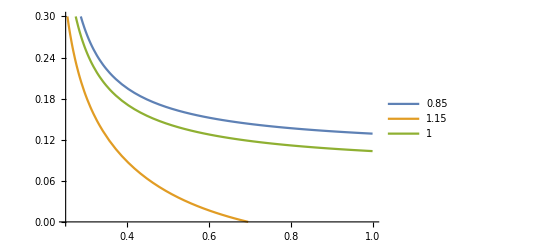

```mathematica
(*Reproducing Figure 3*)
GeV=10^9;
InputParameter={Subscript[N, C]->3,Subscript[α, S]->0.47,Subscript[C, F]->4/3,qqC->(-0.24)^3*GeV^3,ggC->0.012*GeV^4,qGC->0.8*(-0.24)^3*GeV^5};

W[m_,x_]:=1-Sum[(x)^k/k! *Exp[-x],{k,0,m}]

W[2,Subscript[ω, th]/M]

LambdaH=-2*Subscript[α, S]/Pi^3*Subscript[N, C]*Subscript[C, F]*M^5*W[4,Subscript[ω, th]/M]-3*Subscript[α, S]/Pi*Subscript[C, F]*M^2*qqC*W[1,Subscript[ω, th]/M]+M/4*ggC*W[0,Subscript[ω, th]/M]-1/4*qGC;

Plot[{(LambdaH/Formfactor)*10^(-18)/.InputParameter/.Subscript[ω, th]->0.85*GeV,(LambdaH/Formfactor)*10^(-18)/.InputParameter/.Subscript[ω, th]->3*GeV,(LambdaH/Formfactor)*10^(-18)/.InputParameter/.Subscript[ω, th]->GeV},{M,0.25*GeV,GeV},PlotLegends->{0.85,1.15,1},PlotRange->{0,0.30}]
```

#### λ_E^2

##### Timelike region ω > 0

```mathematica
Sigma[μ_,ν_]:=I/2*(GA[μ].GA[ν]-GA[ν].GA[μ])
vTensor[μ_,ν_]:=I*(FV[v,μ].GA[ν]-FV[v,ν].GA[μ])
Subscript[Γ, 1]=I*FV[v,ν].FV[v,α].Sigma[μ,α].GA5;
Subscript[Γ, 2]=I*FV[v,σ].FV[v,α].Sigma[ρ,α].GA5;
P=(1+DiracSlash[v])/2;


C1=Subscript[λ, H]^2*TR[Subscript[Γ, 1].P.GA5.Sigma[μ,ν]]+(Subscript[λ, H]^2-Subscript[λ, E]^2)*TR[Subscript[Γ, 1].P.GA5.vTensor[μ,ν]]/.Pair[Momentum[v],Momentum[v]] ->1//Simplify
C2=Subscript[λ, H]^2*TR[GA5.P.Subscript[Γ, 2].Sigma[ρ,σ]]-(Subscript[λ, H]^2-Subscript[λ, E]^2)*TR[GA5.P.Subscript[Γ, 2].vTensor[ρ,σ]]/.Pair[Momentum[v],Momentum[v]] ->1//Simplify

(-I)^2/36*C1*C2
```

6 ⅈ λ_ⅇ^2

6 ⅈ λ_ⅇ^2

λ_ⅇ^4

##### Spacelike region ω < 0

```mathematica
GeV=10^9;
InputParameter={Subscript[N, C]->3,Subscript[α, S]->0.47,Subscript[C, F]->4/3,qqC->(-0.24)^3*GeV^3,ggC->0.012*GeV^4,qGC->0.8*(-0.24)^3*GeV^5};
Sigma[μ_,ν_]:=I/2*(GA[μ].GA[ν]-GA[ν].GA[μ])
vTensor[μ_,ν_]:=I*(FV[v,μ].GA[ν]-FV[v,ν].GA[μ])
Subscript[Γ, 1]=I*FV[v,ν].FV[v,α].Sigma[μ,α].GA5;
Subscript[Γ, 2]=I*FV[v,σ].FV[v,α].Sigma[ρ,α].GA5;
P=(1+DiracSlash[v])/2;


qGCondensate1=I*qGC*ω*Subscript[C, F]*Subscript[α, S]*Log[-ω/μ]/(96*Pi)*((GA[ρ].GA[σ]-GA[σ].GA[ρ]) -2*(FV[v,σ].GA[ρ]-FV[v,ρ].GA[σ]).DiracSlash[v]);
qGCondensate2=I*qGC*ω*Subscript[C, F]*Subscript[α, S]*Log[-ω/μ]/(96*Pi)*((GA[ρ].GA[σ]-GA[σ].GA[ρ]) +2*DiracSlash[v].(FV[v,σ].GA[ρ]-FV[v,ρ].GA[σ]));
qGCondensate=qGCondensate1+qGCondensate2;


(*Der Faktor Pi/Subscript[α, S]in ggC kommt wegen der definition von Gluon Kondensat <Subscript[α, S]/Pi*G^2>*)
uptodim3=TR[Subscript[Γ, 1].P.Subscript[Γ, 2].DiracSlash[v]].LL+TR[Subscript[Γ, 1].P.Subscript[Γ, 2]].QQCondensate*qqC//Contract;

uptodim4=TR[Subscript[Γ, 1].P.Subscript[Γ, 2].DiracSlash[v]].LL+TR[Subscript[Γ, 1].P.Subscript[Γ, 2]].QQCondensate*qqC+TR[Subscript[Γ, 1].P.Subscript[Γ, 2].DiracSlash[v]].Coefficient[GGCondensate,DiracSlash[v]]*ggC*Pi/Subscript[α, S]//Contract;


uptodim5=TR[Subscript[Γ, 1].P.Subscript[Γ, 2].DiracSlash[v]].LL+TR[Subscript[Γ, 1].P.Subscript[Γ, 2]].QQCondensate*qqC+TR[Subscript[Γ, 1].P.Subscript[Γ, 2]].QQCondensateDim5*qGC+TR[Subscript[Γ, 1].P.Subscript[Γ, 2].DiracSlash[v]].Coefficient[GGCondensate,DiracSlash[v]]*ggC*Pi/Subscript[α, S]+TR[Subscript[Γ, 1].P.Subscript[Γ, 2].Sigma[μ,ν].qGCondensate]//Contract;



(*====================Imaginary-Part================================*)
uptodim3=uptodim3/.Pair[Momentum[v],Momentum[v]] ->1/.Log[-ω/μ]->(-HeavisideTheta[ω])//Simplify;
uptodim4=uptodim4/.Pair[Momentum[v],Momentum[v]] ->1/.Log[-ω/μ]->(-HeavisideTheta[ω])//Simplify;
uptodim5=uptodim5/.Pair[Momentum[v],Momentum[v]] ->1/.Log[-ω/μ]->(-HeavisideTheta[ω])//Expand//Simplify
(*====================Imaginary-Part================================*)

uptodim3=Integrate[uptodim3*Exp[-ω/M],{ω,0,Subscript[ω, th]},GenerateConditions->False]//Simplify;
uptodim4=Integrate[uptodim4*Exp[-ω/M],{ω,0,Subscript[ω, th]},GenerateConditions->False]//Simplify;
uptodim5=Integrate[uptodim5*Exp[-ω/M],{ω,0,Subscript[ω, th]},Assumptions->{0<Subscript[ω, th]<GeV,0<M<GeV},GenerateConditions->False]//Simplify;
```

(2 (v̄)^ν (v̄)^σ ((ḡ)^μρ-4 (v̄)^μ (v̄)^ρ)).(-(ω^6 C_F N_C ω α_S ((ḡ)^μσ ((ḡ)^νρ-2 (v̄)^ν (v̄)^ρ)+2 (v̄)^μ ((v̄)^ρ (ḡ)^νσ-(v̄)^σ (ḡ)^νρ)-(ḡ)^μρ ((ḡ)^νσ-2 (v̄)^ν (v̄)^σ)))/(360 π^3))+qGC (-6 (v̄)^ν (v̄)^σ (ḡ)^μρ).(ω C_F ω α_S ((ḡ)^μρ.(ḡ)^νσ-(ḡ)^μσ.(ḡ)^νρ))/(24 π)+(π ggC (2 (v̄)^ν (v̄)^σ ((ḡ)^μρ-4 (v̄)^μ (v̄)^ρ)).0)/α_S+qqC (-6 (v̄)^ν (v̄)^σ (ḡ)^μρ).0

```mathematica
p2=Plot[{Sqrt[(uptodim5/Formfactor)]*10^(-18)/.InputParameter/.Subscript[ω, th]->0.85*GeV,
Sqrt[(uptodim5/Formfactor)]*10^(-18)/.InputParameter/.Subscript[ω, th]->1.0GeV,Sqrt[(uptodim5/Formfactor)]*10^(-18)/.InputParameter/.Subscript[ω, th]->1.15GeV},{M,0.25*GeV,1GeV},PlotLegends->{"ω_th= 0.85 GeV","ω_th= 1.0 GeV"," ω_th= 1.15 GeV"},AxesLabel->{M,Subscript[λ, E]^2},PlotRange->{0,0.15}]
```

NIntegrate::inumr: The integrand ⅇ^(-3.99975×10^-9 ω) (-1.3824×10^25 (-6 (ḡ)^μρ (v̄)^ν (v̄)^σ).0-1.10592×10^43 (-6 (ḡ)^μρ (v̄)^ν (v̄)^σ).(0.00831142 «2» ω)+«1»+(2 (v̄)^ν ((ḡ)^μρ-4 OverBar[«1»]^(«1») OverBar[«1»]^(«1»)) (v̄)^σ).(-0.000168425 «3»)) has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 8.5×10^8).

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

-Graphics-

```mathematica
Sqrt[(uptodim5/Formfactor)]*10^(-18)/.InputParameter/.Subscript[ω, th]->1.0GeV/.M->0.4*GeV
```

1.91555×10^-31 √Integrate[ⅇ^(-2.5×10^-9 ω) ((2 (v̄)^ν (v̄)^σ ((ḡ)^μρ-4 (v̄)^μ (v̄)^ρ)).(-0.000168425 ω^6 ω ((ḡ)^μσ ((ḡ)^νρ-2 (v̄)^ν (v̄)^ρ)+2 (v̄)^μ ((v̄)^ρ (ḡ)^νσ-(v̄)^σ (ḡ)^νρ)-(ḡ)^μρ ((ḡ)^νσ-2 (v̄)^ν (v̄)^σ)))-1.10592×10^43 (-6 (v̄)^ν (v̄)^σ (ḡ)^μρ).(0.00831142 ω ω ((ḡ)^μρ.(ḡ)^νσ-(ḡ)^μσ.(ḡ)^νρ))-1.3824×10^25 (-6 (v̄)^ν (v̄)^σ (ḡ)^μρ).0+8.02109×10^34 (2 (v̄)^ν (v̄)^σ ((ḡ)^μρ-4 (v̄)^μ (v̄)^ρ)).0),{ω,0,1.×10^9},Assumptions→False,GenerateConditions→False]

#### λ_H^2

##### Timelike region ω >0

```mathematica
Sigma[μ_,ν_]:=I/2*(GA[μ].GA[ν]-GA[ν].GA[μ])
vTensor[μ_,ν_]:=I*(FV[v,μ].GA[ν]-FV[v,ν].GA[μ])
Subscript[Γ, 1]=I*(1/2*Sigma[μ,ν]-FV[v,ν].FV[v,α].Sigma[μ,α]).GA5;
Subscript[Γ, 2]=I*(1/2*Sigma[ρ,σ]-FV[v,σ].FV[v,α].Sigma[ρ,α]).GA5;
P=(1+DiracSlash[v])/2;
(*C1 = -Subscript[λ, H]*TR[Sigma[μ,ν].Subscript[Γ, 1].P.Subscript[Γ, 2].Sigma[ρ,σ]]
C2=Subscript[λ, H]*(Subscript[λ, H]-Subscript[λ, E])*TR[Sigma[μ,ν].Subscript[Γ, 1].P.Subscript[Γ, 2].vTensor[ρ,σ]]
C3=-Subscript[λ, H]*(Subscript[λ, H]-Subscript[λ, E])*TR[vTensor[μ,ν].Subscript[Γ, 1].P.Subscript[Γ, 2].Sigma[ρ,σ]]
C4=(Subscript[λ, H]-Subscript[λ, E])*TR[vTensor[μ,ν].Subscript[Γ, 1].P.Subscript[Γ, 2].vTensor[ρ,σ]]
*)

C1=Subscript[λ, H]*TR[Subscript[Γ, 1].P.GA5.Sigma[μ,ν]]+(Subscript[λ, H]-Subscript[λ, E])*TR[Subscript[Γ, 1].P.GA5.vTensor[μ,ν]]/.Pair[Momentum[v],Momentum[v]] ->1//Simplify;
C2=Subscript[λ, H]*TR[GA5.P.Subscript[Γ, 2].Sigma[ρ,σ]]-(Subscript[λ, H]-Subscript[λ, E])*TR[GA5.P.Subscript[Γ, 2].vTensor[ρ,σ]]/.Pair[Momentum[v],Momentum[v]] ->1//Simplify;

(-I)^2/36*C1*C2//Simplify
```

λ_H^2

##### Spacelike region ω <0

```mathematica
(*TR[Subscript[Γ, 1].P.Subscript[Γ, 2].DiracSlash[v]].Coefficient[GGCondensate,DiracSlash[v]]*ggC*Pi/Subscript[α, S]*)
```

```mathematica
GeV=10^9;
InputParameter={Subscript[N, C]->3,Subscript[α, S]->0.47,Subscript[C, F]->4/3,qqC->(-0.24)^3*GeV^3,ggC->0.012*GeV^4,qGC->0.8*(-0.24)^3*GeV^5};
Sigma[μ_,ν_]:=I/2*(GA[μ].GA[ν]-GA[ν].GA[μ])
vTensor[μ_,ν_]:=I*(FV[v,μ].GA[ν]-FV[v,ν].GA[μ])
Subscript[Γ, 1]=I*(1/2*Sigma[μ,ν]-FV[v,ν].FV[v,α].Sigma[μ,α]).GA5;
Subscript[Γ, 2]=I*(1/2*Sigma[ρ,σ]-FV[v,σ].FV[v,α].Sigma[ρ,α]).GA5;
P=(1+DiracSlash[v])/2;


qGCondensate1=I*qGC*ω*Subscript[C, F]*Subscript[α, S]*Log[-ω/μ]/(96*Pi)*((GA[ρ].GA[σ]-GA[σ].GA[ρ]) +2*(FV[v,σ].GA[ρ]-FV[v,ρ].GA[σ]).DiracSlash[v]);
qGCondensate2=I*qGC*ω*Subscript[C, F]*Subscript[α, S]*Log[-ω/μ]/(96*Pi)*((GA[ρ].GA[σ]-GA[σ].GA[ρ]) +2*DiracSlash[v].(FV[v,σ].GA[ρ]-FV[v,ρ].GA[σ]));


(*qGCondensate1=-I*ω*Subscript[C, F]*Subscript[α, S]*Log[-ω/μ]*(GA[σ].FV[v,ρ]-GA[ρ].FV[v,σ]).DiracSlash[v];
qGCondensate2=-I*ω*Subscript[C, F]*Subscript[α, S]*Log[-ω/μ]*DiracSlash[v].(GA[σ].FV[v,ρ]-GA[ρ].FV[v,σ]);*)

qGCondensate=qGCondensate1+qGCondensate2;

(*Der Faktor Pi/Subscript[α, S]in ggC kommt wegen der definition von Gluon Kondensat <Subscript[α, S]/Pi*G^2>*)
uptodim3=TR[Subscript[Γ, 1].P.Subscript[Γ, 2].DiracSlash[v]].LL+TR[Subscript[Γ, 1].P.Subscript[Γ, 2]].QQCondensate*qqC//Contract;

uptodim4=TR[Subscript[Γ, 1].P.Subscript[Γ, 2].DiracSlash[v]].LL+TR[Subscript[Γ, 1].P.Subscript[Γ, 2]].QQCondensate*qqC+TR[Subscript[Γ, 1].P.Subscript[Γ, 2].DiracSlash[v]].Coefficient[GGCondensate,DiracSlash[v]]*ggC*Pi/Subscript[α, S]//Contract;


uptodim5=TR[Subscript[Γ, 1].P.Subscript[Γ, 2].DiracSlash[v]].LL+TR[Subscript[Γ, 1].P.Subscript[Γ, 2]].QQCondensate*qqC+TR[Subscript[Γ, 1].P.Subscript[Γ, 2]].QQCondensateDim5*qGC+TR[Subscript[Γ, 1].P.Subscript[Γ, 2].DiracSlash[v]].Coefficient[GGCondensate,DiracSlash[v]]*ggC*Pi/Subscript[α, S]+TR[Subscript[Γ, 1].P.Subscript[Γ, 2].Sigma[μ,ν].qGCondensate]//Contract;


(*====================Imaginary-Part================================*)
uptodim3=uptodim3/.Pair[Momentum[v],Momentum[v]] ->1/.Log[-ω/μ]->(-HeavisideTheta[ω])//Simplify;
uptodim4=uptodim4/.Pair[Momentum[v],Momentum[v]] ->1/.Log[-ω/μ]->(-HeavisideTheta[ω])//Simplify;
uptodim5=uptodim5/.Pair[Momentum[v],Momentum[v]] ->1/.Log[-ω/μ]->(-HeavisideTheta[ω])//Simplify;
(*====================Imaginary-Part================================*)

(*uptodim3=Integrate[uptodim3*Exp[-ω/M],{ω,0,Subscript[ω, th]},Assumptions->{0<Subscript[ω, th]<GeV,0<M<GeV},GenerateConditions->False]//Simplify;
uptodim4=Integrate[uptodim4*Exp[-ω/M],{ω,0,Subscript[ω, th]},Assumptions->{0<Subscript[ω, th]<GeV,0<M<GeV},GenerateConditions->False]//Simplify;
uptodim5=Integrate[uptodim5*Exp[-ω/M],{ω,0,Subscript[ω, th]},Assumptions->{0<Subscript[ω, th]<GeV,0<M<GeV},GenerateConditions->False]//Simplify;*)
```

```mathematica
p1=Plot[{Sqrt[(uptodim3/Formfactor)]*10^(-18)/.InputParameter/.Subscript[ω, th]->1.0GeV,Sqrt[(uptodim4/Formfactor)]*10^(-18)/.InputParameter/.Subscript[ω, th]->1.0GeV,
Sqrt[(uptodim5/Formfactor)]*10^(-18)/.InputParameter/.Subscript[ω, th]->1.0GeV},{M,0.25*GeV,GeV},PlotLegends->{"Up to Dim3","Up to Dim4","Up to Dim5"},PlotRange->{0,0.15},AxesLabel->{M,Subscript[λ, H]^2}]

p2=Plot[{Sqrt[(uptodim5/Formfactor)]*10^(-18)/.InputParameter/.Subscript[ω, th]->0.85*GeV,
Sqrt[(uptodim5/Formfactor)]*10^(-18)/.InputParameter/.Subscript[ω, th]->1.0GeV,Sqrt[(uptodim5/Formfactor)]*10^(-18)/.InputParameter/.Subscript[ω, th]->1.15*GeV},{M,0.25*GeV,GeV},PlotLegends->{"ω_th= 0.85 GeV","ω_th= 1.0 GeV"," ω_th= 1.15 GeV"},PlotRange->{0,0.15},AxesLabel->{M,Subscript[λ, H]^2}]
```

-Graphics-

-Graphics-

```mathematica
Sqrt[(uptodim5/Formfactor)]*10^(-18)/.InputParameter/.Subscript[ω, th]->1.0GeV/.M->0.4*GeV
```

3.51569×10^-33 √(-(-3 ω^6-3.2745×10^45 ω) ω)

Find optimal values of ω_th and M

```mathematica
numerator=Integrate[uptodim5*Exp[-ω/M]*ω,{ω,0,Subscript[ω, th]},Assumptions->{0<Subscript[ω, th]<GeV,0<M<GeV},GenerateConditions->False]//Simplify;
denominator=Integrate[uptodim5*Exp[-ω/M],{ω,0,Subscript[ω, th]},Assumptions->{0<Subscript[ω, th]<GeV,0<M<GeV},GenerateConditions->False]//Simplify;
```

```mathematica
exp=(numerator/denominator)/.InputParameter;
Do[Do[Print[Abs[0.55*10^9-exp]/.Subscript[ω, th]->ω1/.M->M1],{M1,0,1*GeV,0.05*GeV}],{ω1,0,2*GeV,0.05*GeV}]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Indeterminate

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Indeterminate

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Indeterminate

Indeterminate

Indeterminate

«17 more identical outputs»

5.19611×10^8

5.181×10^8

5.17613×10^8

5.17372×10^8

5.17229×10^8

5.17135×10^8

5.17067×10^8

5.17017×10^8

5.16978×10^8

5.16946×10^8

5.16921×10^8

5.16899×10^8

5.16881×10^8

5.16866×10^8

5.16853×10^8

5.16841×10^8

5.16831×10^8

5.16822×10^8

5.16813×10^8

5.16806×10^8

Indeterminate

4.95568×10^8

4.89221×10^8

4.87191×10^8

4.86199×10^8

4.85613×10^8

4.85225×10^8

4.8495×10^8

4.84745×10^8

4.84586×10^8

4.84459×10^8

4.84355×10^8

4.84269×10^8

4.84197×10^8

4.84134×10^8

4.84081×10^8

4.84033×10^8

4.83992×10^8

4.83955×10^8

4.83922×10^8

4.83893×10^8

Indeterminate

4.77975×10^8

4.63539×10^8

4.58831×10^8

4.56539×10^8

4.55188×10^8

4.54298×10^8

4.53669×10^8

4.532×10^8

4.52837×10^8

4.52548×10^8

4.52312×10^8

4.52117×10^8

4.51951×10^8

4.5181×10^8

4.51688×10^8

4.51581×10^8

4.51487×10^8

4.51403×10^8

4.51329×10^8

4.51262×10^8

Indeterminate

4.66128×10^8

4.41133×10^8

4.32603×10^8

4.28439×10^8

4.25989×10^8

4.24379×10^8

4.23241×10^8

4.22395×10^8

4.21742×10^8

4.21222×10^8

4.20798×10^8

4.20447×10^8

4.2015×10^8

4.19897×10^8

4.19678×10^8

4.19486×10^8

4.19318×10^8

4.19168×10^8

4.19035×10^8

4.18915×10^8

Indeterminate

4.58772×10^8

4.21973×10^8

4.08547×10^8

4.01934×10^8

3.9804×10^8

3.95484×10^8

3.9368×10^8

3.92341×10^8

3.91307×10^8

3.90485×10^8

3.89817×10^8

3.89262×10^8

3.88794×10^8

3.88395×10^8

3.88049×10^8

3.87748×10^8

3.87483×10^8

3.87248×10^8

3.87038×10^8

3.86849×10^8

Indeterminate

4.5453×10^8

4.05922×10^8

3.86669×10^8

3.77042×10^8

3.71357×10^8

3.67625×10^8

3.64993×10^8

3.6304×10^8

3.61534×10^8

3.60338×10^8

3.59365×10^8

3.58559×10^8

3.57879×10^8

3.57299×10^8

3.56798×10^8

3.56361×10^8

3.55977×10^8

3.55636×10^8

3.55331×10^8

3.55058×10^8

Indeterminate

4.52233×10^8

3.92745×10^8

3.66936×10^8

3.53764×10^8

3.45943×10^8

3.40802×10^8

3.37177×10^8

3.34488×10^8

3.32416×10^8

3.30771×10^8

3.29434×10^8

3.28327×10^8

3.27394×10^8

3.26599×10^8

3.25911×10^8

3.25312×10^8

3.24785×10^8

3.24318×10^8

3.23901×10^8

3.23526×10^8

Indeterminate

4.51051×10^8

3.82134×10^8

3.4928×10^8

3.32077×10^8

3.21785×10^8

3.15003×10^8

3.10218×10^8

3.06669×10^8

3.03935×10^8

3.01766×10^8

3.00004×10^8

2.98544×10^8

2.97316×10^8

2.96269×10^8

2.95365×10^8

2.94576×10^8

2.93883×10^8

2.93269×10^8

2.92721×10^8

2.92229×10^8

Indeterminate

4.50468×10^8

3.73743×10^8

3.33598×10^8

3.11939×10^8

2.98853×10^8

2.902×10^8

2.84087×10^8

2.79551×10^8

2.76058×10^8

2.73288×10^8

2.71038×10^8

2.69175×10^8

2.67609×10^8

2.66273×10^8

2.6512×10^8

2.64115×10^8

2.63232×10^8

2.6245×10^8

2.61752×10^8

2.61125×10^8

Indeterminate

4.50189×10^8

3.67212×10^8

3.19758×10^8

2.93286×10^8

2.771×10^8

2.66347×10^8

2.58738×10^8

2.53088×10^8

2.48737×10^8

2.45286×10^8

2.42484×10^8

2.40166×10^8

2.38216×10^8

2.36554×10^8

2.35121×10^8

2.33872×10^8

2.32775×10^8

2.31803×10^8

2.30936×10^8

2.30158×10^8

Indeterminate

4.50058×10^8

3.62196×10^8

3.07606×10^8

2.7603×10^8

2.56457×10^8

2.43381×10^8

2.34104×10^8

2.27211×10^8

2.219×10^8

2.17688×10^8

2.1427×10^8

2.11441×10^8

2.09064×10^8

2.07037×10^8

2.0529×10^8

2.03768×10^8

2.02431×10^8

2.01248×10^8

2.00192×10^8

1.99245×10^8

Indeterminate

4.49998×10^8

3.58384×10^8

2.96972×10^8

2.6007×10^8

2.36837×10^8

2.21215×10^8

2.101×10^8

2.0183×10^8

1.95455×10^8

1.90399×10^8

1.86296×10^8

1.82902×10^8

1.8005×10^8

1.77619×10^8

1.75525×10^8

1.73701×10^8

1.72099×10^8

1.70681×10^8

1.69416×10^8

1.68283×10^8

Indeterminate

4.49971×10^8

3.55511×10^8

2.87685×10^8

2.45286×10^8

2.18138×10^8

1.99745×10^8

1.86616×10^8

1.76832×10^8

1.69286×10^8

1.633×10^8

1.58442×10^8

1.54424×10^8

1.51049×10^8

1.48174×10^8

1.45696×10^8

1.4354×10^8

1.41646×10^8

1.3997×10^8

1.38477×10^8

1.37138×10^8

Indeterminate

4.49959×10^8

3.53354×10^8

2.7957×10^8

2.31552×10^8

2.00239×10^8

1.7885×10^8

1.63523×10^8

1.52082×10^8

1.4325×10^8

1.36244×10^8

1.30558×10^8

1.25857×10^8

1.21908×10^8

1.18545×10^8

1.15649×10^8

1.13129×10^8

1.10916×10^8

1.08959×10^8

1.07215×10^8

1.05651×10^8

Indeterminate

4.49953×10^8

3.51738×10^8

2.72467×10^8

2.18738×10^8

1.83011×10^8

1.5839×10^8

1.40674×10^8

1.27424×10^8

1.17187×10^8

1.09065×10^8

1.02474×10^8

9.70256×10^7

9.24502×10^7

8.85559×10^7

8.52025×10^7

8.22856×10^7

7.97259×10^7

7.7462×10^7

7.54457×10^7

7.36387×10^7

Indeterminate

4.49951×10^8

3.50526×10^8

2.66226×10^8

2.06712×10^8

1.66321×10^8

1.38218×10^8

1.17906×10^8

1.02685×10^8

9.09165×10^7

8.1576×10^7

7.39983×10^7

6.7736×10^7

6.24791×10^7

5.80065×10^7

5.41569×10^7

5.08098×10^7

4.78737×10^7

4.52779×10^7

4.29669×10^7

4.08965×10^7

Indeterminate

4.49949×10^8

3.49616×10^8

2.60715×10^8

1.95353×10^8

1.50032×10^8

1.18179×10^8

9.5051×10^7

7.76835×10^7

6.42458×10^7

5.35796×10^7

4.49284×10^7

3.7782×10^7

3.17858×10^7

2.6687×10^7

2.23006×10^7

1.84887×10^7

1.51466×10^7

1.21931×10^7

9.56486×10^6

7.21124×10^6

Indeterminate

4.49949×10^8

3.48928×10^8

2.55822×10^8

1.84547×10^8

1.34014×10^8

9.81221×10^7

7.19364×10^7

5.22342×10^7

3.69807×10^7

2.4874×10^7

1.50586×10^7

6.95507×10^6

160193.

5.61408×10^6

1.05783×10^7

1.48896×10^7

1.86674×10^7

2.2004×10^7

2.49716×10^7

2.76278×10^7

Indeterminate

4.49949×10^8

3.48408×10^8

2.51452×10^8

1.74196×10^8

1.18148×10^8

7.79011×10^7

4.83972×10^7

2.61575×10^7

8.9326×10^6

4.73465×10^6

1.58084×10^7

2.49436×10^7

3.25972×10^7

3.90959×10^7

4.46784×10^7

4.95229×10^7

5.37649×10^7

5.75089×10^7

6.08369×10^7

6.38138×10^7

Indeterminate

4.49949×10^8

3.48011×10^8

2.47528×10^8

1.64217×10^8

1.02327×10^8

5.73845×10^7

2.42819×10^7

710764.

2.00701×10^7

3.54218×10^7

4.78491×10^7

5.80902×10^7

6.66613×10^7

7.39314×10^7

8.01705×10^7

8.55797×10^7

9.0312×10^7

9.44855×10^7

9.81923×10^7

1.01506×10^8

Indeterminate

4.49949×10^8

3.47708×10^8

2.43988×10^8

1.54543×10^8

8.64648×10^7

3.646×10^7

540151.

2.85115×10^7

5.01726×10^7

6.73332×10^7

8.12075×10^7

9.26258×10^7

1.02169×10^8

1.10254×10^8

1.17184×10^8

1.23185×10^8

1.2843×10^8

1.33051×10^8

1.37152×10^8

1.40814×10^8

Indeterminate

4.49948×10^8

3.47476×10^8

2.40782×10^8

1.45127×10^8

7.04933×10^7

1.50382×10^7

2.61727×10^7

5.73546×10^7

8.14852×10^7

1.00576×10^8

1.15985×10^8

1.28646×10^8

1.39211×10^8

1.48147×10^8

1.55795×10^8

1.6241×10^8

1.68184×10^8

1.73265×10^8

1.7777×10^8

1.8179×10^8

Indeterminate

4.49948×10^8

3.47298×10^8

2.37873×10^8

1.35934×10^8

5.43666×10^7

6.94442×10^6

5.26885×10^7

8.73139×10^7

1.14077×10^8

1.35211×10^8

1.52235×10^8

1.66194×10^8

1.77819×10^8

1.87634×10^8

1.96021×10^8

2.03263×10^8

2.09575×10^8

2.15124×10^8

2.20037×10^8

2.24416×10^8

Indeterminate

4.49948×10^8

3.47161×10^8

2.3523×10^8

1.26945×10^8

3.80591×10^7

2.95244×10^7

8.01276×10^7

1.18425×10^8

1.47974×10^8

1.71253×10^8

1.89958×10^8

2.05258×10^8

2.17971×10^8

2.28682×10^8

2.37817×10^8

2.45691×10^8

2.52544×10^8

2.58558×10^8

2.63877×10^8

2.68612×10^8

Indeterminate

4.49948×10^8

3.47055×10^8

2.32829×10^8

1.18154×10^8

2.15649×10^7

5.27117×10^7

1.08497×10^8

1.50683×10^8

1.83157×10^8

2.08667×10^8

2.29104×10^8

2.45774×10^8

2.59589×10^8

2.71201×10^8

2.81083×10^8

2.89585×10^8

2.96971×10^8

3.03443×10^8

3.09157×10^8

3.14238×10^8

Indeterminate

4.49948×10^8

3.46975×10^8

2.30651×10^8

1.09561×10^8

4.89556×10^6

7.64918×10^7

1.37772×10^8

1.84049×10^8

2.19567×10^8

2.47375×10^8

2.69578×10^8

2.87631×10^8

3.02549×10^8

3.15055×10^8

3.25672×10^8

3.34787×10^8

3.42691×10^8

3.49604×10^8

3.55699×10^8

3.6111×10^8

Indeterminate

4.49948×10^8

3.46913×10^8

2.2868×10^8

1.01176×10^8

1.19225×10^7

1.00828×10^8

1.67902×10^8

2.18452×10^8

2.57113×10^8

2.87264×10^8

3.11248×10^8

3.3068×10^8

3.46688×10^8

3.60068×10^8

3.714×10^8

3.81106×10^8

3.89505×10^8

3.96837×10^8

4.03291×10^8

4.09013×10^8

Indeterminate

4.49948×10^8

3.46866×10^8

2.269×10^8

9.30151×10^7

2.88508×10^7

1.25667×10^8

1.98812×10^8

2.53793×10^8

2.95674×10^8

3.28194×10^8

3.53956×10^8

3.74749×10^8

3.9182×10^8

4.06047×10^8

4.18062×10^8

4.2833×10^8

4.37195×10^8

4.44921×10^8

4.51708×10^8

4.57716×10^8

Indeterminate

4.49948×10^8

3.4683×10^8

2.25299×10^8

8.50943×10^7

4.58417×10^7

1.50938×10^8

2.3041×10^8

2.89957×10^8

3.35109×10^8

3.70005×10^8

3.97526×10^8

4.1965×10^8

4.37749×10^8

4.52785×10^8

4.65448×10^8

4.76242×10^8

4.85542×10^8

4.9363×10^8

5.00724×10^8

5.06993×10^8

Indeterminate

4.49948×10^8

3.46803×10^8

2.23865×10^8

7.74326×10^7

6.28413×10^7

1.76563×10^8

2.62592×10^8

3.26814×10^8

3.7527×10^8

4.1253×10^8

4.41778×10^8

4.65192×10^8

4.84275×10^8

5.00077×10^8

5.13348×10^8

5.24632×10^8

5.34332×10^8

5.42751×10^8

5.50123×10^8

5.56627×10^8

Indeterminate

4.49948×10^8

3.46782×10^8

2.22585×10^8

7.00488×10^7

7.9792×10^7

2.02456×10^8

2.95247×10^8

3.6423×10^8

4.16002×10^8

4.556×10^8

4.86533×10^8

5.11189×10^8

5.31209×10^8

5.47732×10^8

5.61569×10^8

5.73304×10^8

5.83369×10^8

5.92089×10^8

5.9971×10^8

6.06424×10^8

Indeterminate

4.49948×10^8

3.46767×10^8

2.21448×10^8

6.29601×10^7

9.66345×10^7

2.28526×10^8

3.28258×10^8

4.02069×10^8

4.57153×10^8

4.99053×10^8

5.31621×10^8

5.57468×10^8

5.78375×10^8

5.95573×10^8

6.09934×10^8

6.22084×10^8

6.32482×10^8

6.41473×10^8

6.49317×10^8

6.56218×10^8

Indeterminate

4.49948×10^8

3.46755×10^8

2.20443×10^8

5.61817×10^7

1.1331×10^8

2.54684×10^8

3.61513×10^8

4.40198×10^8

4.98579×10^8

5.42738×10^8

5.76888×10^8

6.03873×10^8

6.25617×10^8

6.43447×10^8

6.58293×10^8

6.70823×10^8

6.81524×10^8

6.90759×10^8

6.98803×10^8

7.05869×10^8

Indeterminate

4.49948×10^8

3.46747×10^8

2.19557×10^8

4.9726×10^7

1.29762×10^8

2.80842×10^8

3.949×10^8

4.78491×10^8

5.40145×10^8

5.86515×10^8

6.22195×10^8

6.50266×10^8

6.72802×10^8

6.91222×10^8

7.06518×10^8

7.19397×10^8

7.30374×10^8

7.3983×10^8

7.48055×10^8

7.55269×10^8

Indeterminate

4.49948×10^8

3.4674×10^8

2.18782×10^8

4.36025×10^7

1.45936×10^8

3.06914×10^8

4.28315×10^8

5.16834×10^8

5.81731×10^8

6.30264×10^8

6.67422×10^8

6.96532×10^8

7.19817×10^8

7.38791×10^8

7.54506×10^8

7.67708×10^8

7.78938×10^8

7.88597×10^8

7.96985×10^8

8.04333×10^8

Indeterminate

4.49948×10^8

3.46736×10^8

2.18105×10^8

3.78172×10^7

1.61784×10^8

3.3282×10^8

4.6166×10^8

5.5512×10^8

6.23229×10^8

6.73878×10^8

7.12467×10^8

7.42572×10^8

7.6657×10^8

7.86067×10^8

8.02175×10^8

8.15679×10^8

8.27145×10^8

8.3699×10^8

8.45529×10^8

8.52999×10^8

Indeterminate

4.49948×10^8

3.46732×10^8

2.17517×10^8

3.23732×10^7

1.77259×10^8

3.58486×10^8

4.94848×10^8

5.93255×10^8

6.64544×10^8

7.17267×10^8

7.57246×10^8

7.8831×10^8

8.1299×10^8

8.32985×10^8

8.49466×10^8

8.63254×10^8

8.74941×10^8

8.84962×10^8

8.93642×10^8

9.01228×10^8

Indeterminate

4.49948×10^8

3.4673×10^8

2.17009×10^8

2.72701×10^7

1.92323×10^8

3.83844×10^8

5.27796×10^8

6.31155×10^8

7.05596×10^8

7.60356×10^8

8.01689×10^8

8.33683×10^8

8.59021×10^8

8.79495×10^8

8.96332×10^8

9.10393×10^8

9.22293×10^8

9.32482×10^8

9.41297×10^8

9.48993×10^8

Indeterminate

4.49948×10^8

3.46728×10^8

2.16571×10^8

2.25048×10^7

2.0694×10^8

4.08833×10^8

5.60433×10^8

6.68748×10^8

7.46318×10^8

8.03085×10^8

8.45744×10^8

8.78645×10^8

9.04622×10^8

9.25561×10^8

9.42745×10^8

9.57071×10^8

9.69178×10^8

9.79531×10^8

9.88479×10^8

9.96283×10^8

Indeterminate

4.49948×10^8

3.46727×10^8

2.16196×10^8

1.80716×10^7

2.21081×10^8

4.33396×10^8

5.92696×10^8

7.05971×10^8

7.86652×10^8

8.45403×10^8

8.89368×10^8

9.23159×10^8

9.49764×10^8

9.7116×10^8

9.88686×10^8

1.00327×10^9

1.01558×10^9

1.0261×10^9

1.03518×10^9

1.0431×10^9

```mathematica
ClearAll[Subscript[ω, th],M];
Case = {exp=numerator/denominator/.InputParameter;

If[Abs[0.55*10^8-exp]≤0.5*GeV,Print[exp] ];}

Abs[exp]/.Subscript[ω, th]->1.0*GeV/.M->0.5GeV


Do[For[Subscript[ω, th]=0,Subscript[ω, th]<2*GeV,Subscript[ω, th]=Subscript[ω, th]+0.1*GeV,Case],{M,0,1*GeV,0.1*GeV}]
```

{Null}

Abs[Integrate[(ⅇ^(-2.×10^-9 ω) ω^2 (0.626667 (3 ω^5-30 π^2 (-2.7648×10^25 ω^2-1.10592×10^43))+5.58113×10^36 ω) ω)/(60 π^3),{ω,0,1.×10^9},Assumptions→False,GenerateConditions→False]/Integrate[(ⅇ^(-2.×10^-9 ω) ω (0.626667 (3 ω^5-30 π^2 (-2.7648×10^25 ω^2-1.10592×10^43))+5.58113×10^36 ω) ω)/(60 π^3),{ω,0,1.×10^9},Assumptions→False,GenerateConditions→False]]